```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
Integrate[x^2*1/x,{x,0,1}]
```

1/2

```mathematica
2*Integrate[x*(1-x)*1/x,{x,0,1}]
```

1

```mathematica
-x*D[x^2,x]+1/2*x*(1-x)*D[x^2,{x,2}]//FullSimplify
```

x-3 x^2

```mathematica
-x*D[x*(1-x),x]+1/2*x*(1-x)*D[x*(1-x),{x,2}]
```

-(1-2 x) x-(1-x) x

```mathematica
DSolve[{D[f[t],t]==-f[t],f[0]==x0},f,t]
```

{{f→Function[{t},ⅇ^-t x0]}}

```mathematica
DSolve[{D[f[t],t]==x0*Exp[-t]-3*f[t],f[0]==x0^2},f,t]
```

{{f→Function[{t},1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)]}}

```mathematica
1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)//FullSimplify
```

```mathematica
pHom = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)
```

1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)

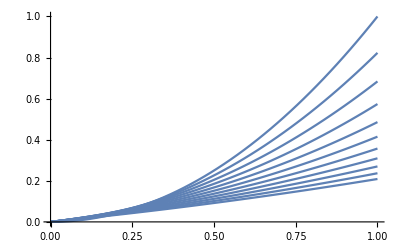

```mathematica
Plot[Table[1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHet = 2*(x0*Exp[-t]-pHom)//FullSimplify
```

ⅇ^(-3 t) (1+ⅇ^(2 t)-2 x0) x0

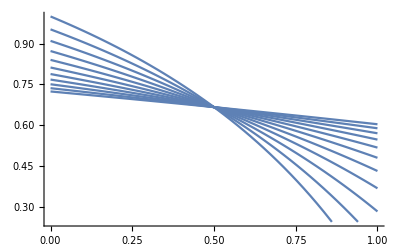

```mathematica
Plot[Table[pHet/(pHet+pHom),{t,0,1,.1}],{x0,0,1}]
```

```mathematica
pHetgHetHom = pHet/(pHet+pHom)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t)-2 x0))

```mathematica
pHetAncTable = Table[Table[pHetgHetHom,{x0,.01,.99,.01}],{t,0,1,.1}];
```

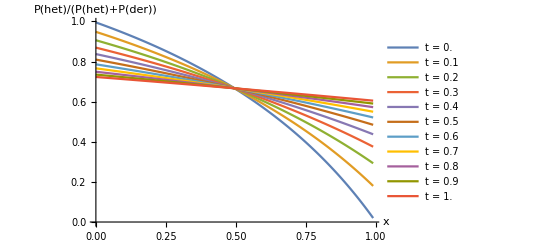

```mathematica
ListLinePlot[pHetAncTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t = ``",ti],{ti,0,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

```mathematica
pHetgHetHom/.{t->.01,x0->.01}
```

0.990051

```mathematica
ExAnc = ⅇ^-t x0/.t->t1
```

ⅇ^-t1 x0

```mathematica
Ex2Anc = 1/2 ⅇ^(-3 t) x0 (-1+ⅇ^(2 t)+2 x0)/.t->t1
```

1/2 ⅇ^(-3 t1) x0 (-1+ⅇ^(2 t1)+2 x0)

```mathematica
ExSplit = x0*Exp[-t1]
```

ⅇ^-t1 x0

```mathematica
Ex2Split = (Exp[-t1]-1/2*Exp[-(3*t1+t2)]-1/2*Exp[-(t1+t2)])*x0+Exp[-(3*t1+t2)]*x0^2
```

(ⅇ^-t1-1/2 ⅇ^(-3 t1-t2)-ⅇ^(-t1-t2)/2) x0+ⅇ^(-3 t1-t2) x0^2

```mathematica
pHetgHetHomSplit = 1-Ex2Split/(2*ExSplit-Ex2Split)//FullSimplify
```

1/(1/2+ⅇ^(2 t1+t2)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetgHetHomAnc = 1-Ex2Anc/(2*ExAnc-Ex2Anc)//FullSimplify
```

1/(3/2+(-1+2 x0)/(1+ⅇ^(2 t1)-2 x0))

```mathematica
pHetSplitTable = Table[Table[pHetgHetHomSplit/.t2->t1-.1,{x0,.01,.99,.01}],{t1,.1,1,.1}];
```

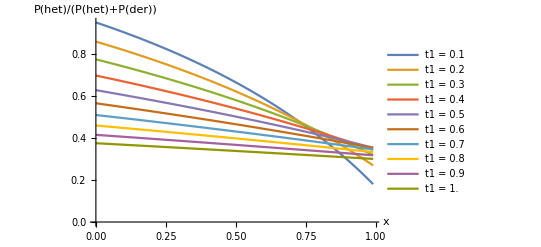

```mathematica
ListLinePlot[pHetSplitTable,PlotRange->All,DataRange->{.0,.99},PlotLegends->Table[StringForm["t1 = ``",ti],{ti,.1,1,.1}],AxesLabel->{"x","P(het)/(P(het)+P(der))"}]
```

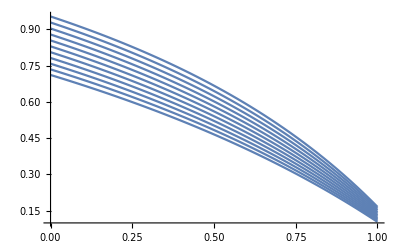

```mathematica
Plot[Table[pHetgHetHomSplit/.t1->0.1,{t2,0,.5,.05}],{x0,0,1}]
```

```mathematica
blah = pHetgHetHomAnc/pHetgHetHomSplit//FullSimplify
```

(1+ⅇ^(2 t1) (1+2 ⅇ^t2)-2 x0)/(1+3 ⅇ^(2 t1)-2 x0)

```mathematica
3*(3-1)/2
```

3

```mathematica
Q = {{0,0,0},{1,-1,0},{0,3,-3}}
```

```mathematica
{{0,0,0},{1,-1,0},{0,3,-3}}//MatrixForm
```

(0 | 0 | 0
1 | -1 | 0
0 | 3 | -3)

```mathematica
MatrixExp[Q*t].{x,x^2,x^3}//FullSimplify
```

{x,x+ⅇ^-t (-1+x) x,1/2 x (2+ⅇ^(-3 t) (-1+x) (-1+3 ⅇ^(2 t)+2 x))}

```mathematica
-3*(3+1)/2
```

-6

```mathematica
Qd = {{-1,0,0},{1,-3,0},{0,3,-6}}
```

{{-1,0,0},{1,-3,0},{0,3,-6}}

```mathematica
Truth = MatrixExp[Q*t2].MatrixExp[Qd*t1].{x,x^2,x^3}
```

{ⅇ^-t1 x,(1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2,(1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))) x+(ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2))) x^2+ⅇ^(-6 t1-3 t2) x^3}

```mathematica
(Ex2Split/.x0->x)/((1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2)//FullSimplify
```

1

```mathematica
blah  = MatrixExp[Q*t2].MatrixExp[Qd*t1]
```

{{ⅇ^-t1,0,0},{1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2),ⅇ^(-3 t1-t2),0},{1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2)),ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2)),ⅇ^(-6 t1-3 t2)}}

```mathematica
Truth2 = blah.{x,x^2,x^3}
```

{ⅇ^-t1 x,(1/2 ⅇ^(-3 t1-t2) (-1+ⅇ^(2 t1))+ⅇ^(-t1-t2) (-1+ⅇ^t2)) x+ⅇ^(-3 t1-t2) x^2,(1/10 ⅇ^(-6 t1-3 t2) (-1+ⅇ^t1)^2 (2+4 ⅇ^t1+6 ⅇ^(2 t1)+3 ⅇ^(3 t1))+1/2 ⅇ^(-t1-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2)+3/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))) x+(ⅇ^(-6 t1-3 t2) (-1+ⅇ^(3 t1))+3/2 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t2))) x^2+ⅇ^(-6 t1-3 t2) x^3}

```mathematica
Truth3 = blah.Table[Beta[k-1/2+i,n-k-1/2]/Beta[k-1/2,n-k-1/2],{i,1,3}]//FullSimplify
```

{(ⅇ^-t1 (-1+2 k))/(2 (-1+n)),(ⅇ^(-3 t1-t2) (-1+2 k) (1+2 k+(-1+ⅇ^(2 t1) (-1+2 ⅇ^t2)) n))/(4 (-1+n) n),(ⅇ^(-3 (2 t1+t2)) (-1+2 k) (4+ⅇ^(3 t1) (5+ⅇ^(2 t1)+20 ⅇ^(2 t1+3 t2)-15 ⅇ^(2 t2) (1+ⅇ^(2 t1)))+(5 (-2+ⅇ^(3 t1) (-1+3 ⅇ^(2 t2))) (1+2 k))/n+(5 (3+4 k (2+k)))/(n (1+n))))/(40 (-1+n))}

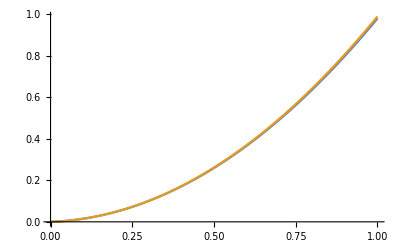

```mathematica
Plot[{Truth[[2]]/.{t1->.01,t2->.05},Truth3[[2]]/.k->x*n/.{n->100,t1->.01,t2->.05}},{x,0,1}]
```

```mathematica
FullSimplify[Beta[k+m,n-k+1]/Beta[k,n-k+1],Assumptions->Element[k,Integers]&&Element[n,Integers]&&Element[m,Integers]&&k>0&&m>0&&n>0]
```

(n! Gamma[k+m])/((m+n)! Gamma[k])

```mathematica
Integrate[x^m*x^(k-1)*(1-x)^(n-k),{x,0,1}]
```

ConditionalExpression[(Gamma[k+m] Gamma[1-k+n])/Gamma[1+m+n],Re[k-n]<1&&Re[k+m]>0]

```mathematica
(* USING THE SAMPLING PROBS EXPLICITLY *)
```

```mathematica
L[f_]:= 1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
Dmunk= L[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)

```mathematica
Ld [f_]:=-x*D[f,x]+1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
Ld[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)-x (k (1-x)^(-k+n) x^(-1+k)-(-k+n) (1-x)^(-1-k+n) x^k)

```mathematica
Dμ[n][k] = 1/2 ((-1+k) k μ[n][k-1]-2 k (-k+n) μ[n,k]+(-1-k+n) (-k+n)μ[n][k+1])
```

1/2 (-2 k (-k+n) μ[n,k]+(-1+k) k μ[n][-1+k]+(-1-k+n) (-k+n) μ[n][1+k])

```mathematica
?Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

```mathematica
makeMatrix[n_]:=Module[{k,i},Table[Table[Piecewise[{{-k*(n-k),i==k},{1/2*k*(k-1),i==k-1},{1/2*(n-k-1)*(n-k),i==k+1}}],{i,1,n}],{k,1,n}]]
```

```mathematica
makeHet[n_]:= Table[x^k*(1-x)^(n-k),{k,1,n}]
```

```mathematica
L[f_]:= 1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
Dmunk= L[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)

```mathematica
Ld [f_]:=-x*D[f,x]+1/2*x*(1-x)*D[f,{x,2}]
```

```mathematica
generatorDown = Ld[x^k*(1-x)^(n-k)]
```

1/2 (1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k)-x (k (1-x)^(-k+n) x^(-1+k)-(-k+n) (1-x)^(-1-k+n) x^k)

```mathematica
Dμ[n][k] = 1/2 ((-1+k) k μ[n][k-1]-2 k (-k+n) μ[n,k]+(-1-k+n) (-k+n)μ[n][k+1])
```

1/2 (-2 k (-k+n) μ[n,k]+(-1+k) k μ[n][-1+k]+(-1-k+n) (-k+n) μ[n][1+k])

```mathematica
?Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

```mathematica
makeQ[n_]:=Module[{k,i},Table[Table[Piecewise[{{-k*(n-k),i==k},{1/2*k*(k-1),i==k-1},{1/2*(n-k-1)*(n-k),i==k+1}}],{i,0,n}],{k,0,n}]]
```

```mathematica
makeHet[n_]:= Table[x^k*(1-x)^(n-k),{k,0,n}]
```

```mathematica
makeQd[n_]:=Module[{k,i},Table[Table[Piecewise[{{-k*(n-k+1),i==k},{1/2*k*(k-1),i==k-1},{1/2*(k-n-1)*(k-n),i==k+1}}],{i,0,n}],{k,0,n}]]
```

```mathematica
makeQmu[n_]:=Module[{k,i}, Table[Table[Piecewise[{{k,i==k-1},{-(n-k),i==k}}],{i,0,n}],{k,0,n}]]
```

```mathematica
makeQmuBoth[n_]:=Module[{k,i},Table[Table[Piecewise[{{α/2*k,i==k-1},{-α/2*(n-k)-β/2*k,i==k},{β/2*(n-k),i==k+1}}],{i,0,n}],{k,0,n}]]
```

```mathematica
makeQs[n_]:=Module[{k,i},Table[Table[Piecewise[{{k,i==k},{-(n-k),i==k+1}}],{i,0,n}],{k,0,n}]]
```

```mathematica
Q = makeQ[3];
```

```mathematica
Qd = makeQd[3];
```

```mathematica
het = makeHet[3];
```

```mathematica
het/.x->.2
```

{0.512,0.128,0.032,0.008}

```mathematica
-(n-k)-k
```

-n

```mathematica
MatrixExp[Q].MatrixExp[Qd].het/.x->.2
```

{0.904217,0.00757474,0.00705773,0.0518857}

```mathematica
Sum[MatrixExp[Q].MatrixExp[Qd].het
```

```mathematica
makeQd[3]
```

{{0,6,0,0},{0,-3,3,0},{0,1,-4,1},{0,0,3,-3}}

```mathematica
1/2*(1-ϵ)+(1-1/2)*ϵ//FullSimplify
```

1/2

```mathematica
((k-n-1)*(k-n))/((n-k)*(n-k+1))//FullSimplify
```

1

```mathematica
L[n!/(k!*(n-k)!)*x^k(1-x)^(n-k)]
```

((1-x) x ((-1+k) k (1-x)^(-k+n) x^(-2+k)-2 k (-k+n) (1-x)^(-1-k+n) x^(-1+k)+(-1-k+n) (-k+n) (1-x)^(-2-k+n) x^k) n!)/(2 k! (-k+n)!)

```mathematica
FullSimplify[(-1+k) k*n!/(k!*(n-k)!),k≤n&&n>0]
```

((-1+k) k n!)/(k! (-k+n)!)

```mathematica
Q1 = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
Q2 = makeQ[4]
```

{{0,6,0,0,0},{0,-3,3,0,0},{0,1,-4,1,0},{0,0,3,-3,0},{0,0,0,6,0}}

```mathematica
h1 = makeHet[3]
```

{(1-x)^3,(1-x)^2 x,(1-x) x^2,x^3}

```mathematica
h2=makeHet[4]
```

{(1-x)^4,(1-x)^3 x,(1-x)^2 x^2,(1-x) x^3,x^4}

```mathematica
p1 = MatrixExp[Q1*t1]
```

{{1,1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1),0},{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0},{0,1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),0},{0,1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1),1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)),1}}

```mathematica
p2 = MatrixExp[Q2*t2]
```

{{1,1/5 ⅇ^(-6 t2) (-1-5 ⅇ^(3 t2)-9 ⅇ^(5 t2)+15 ⅇ^(6 t2)),3+(3 ⅇ^(-6 t2))/5-(18 ⅇ^-t2)/5,1/5 ⅇ^(-6 t2) (-1+ⅇ^t2)^3 (1+3 ⅇ^t2+6 ⅇ^(2 t2)+5 ⅇ^(3 t2)),0},{0,1/10 ⅇ^(-6 t2) (2+5 ⅇ^(3 t2)+3 ⅇ^(5 t2)),3/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/10 ⅇ^(-6 t2) (-1+ⅇ^t2)^2 (2+4 ⅇ^t2+6 ⅇ^(2 t2)+3 ⅇ^(3 t2)),0},{0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0},{0,1/10 ⅇ^(-6 t2) (-1+ⅇ^t2)^2 (2+4 ⅇ^t2+6 ⅇ^(2 t2)+3 ⅇ^(3 t2)),3/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/10 ⅇ^(-6 t2) (2+5 ⅇ^(3 t2)+3 ⅇ^(5 t2)),0},{0,1/5 ⅇ^(-6 t2) (-1+ⅇ^t2)^3 (1+3 ⅇ^t2+6 ⅇ^(2 t2)+5 ⅇ^(3 t2)),3+(3 ⅇ^(-6 t2))/5-(18 ⅇ^-t2)/5,1/5 ⅇ^(-6 t2) (-1-5 ⅇ^(3 t2)-9 ⅇ^(5 t2)+15 ⅇ^(6 t2)),1}}

```mathematica
p1.h1//FullSimplify
```

{-1/2 ⅇ^(-3 t1) (-1+x) (2 ⅇ^(3 t1)-3 ⅇ^(2 t1) x+x (-1+2 x)),-1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)-2 x) (-1+x) x,-1/2 ⅇ^(-3 t1) (-1+x) x (-1+ⅇ^(2 t1)+2 x),1/2 x (2+ⅇ^(-3 t1) (-1+x) (-1+3 ⅇ^(2 t1)+2 x))}

```mathematica
p2.h2//FullSimplify
```

{1/5 ⅇ^(-6 t2) (-1+x) (-5 ⅇ^(6 t2)+x+9 ⅇ^(5 t2) x+5 (-1+x) x^2-5 ⅇ^(3 t2) x (-1+2 x)),-1/10 ⅇ^(-6 t2) (-1+x) x (3 ⅇ^(5 t2)+ⅇ^(3 t2) (5-10 x)+2 (1+5 (-1+x) x)),1/5 ⅇ^(-6 t2) (-1+x) x (1-ⅇ^(5 t2)+5 (-1+x) x),-1/10 ⅇ^(-6 t2) (-1+x) x (3 ⅇ^(5 t2)+5 ⅇ^(3 t2) (-1+2 x)+2 (1+5 (-1+x) x)),1/5 ⅇ^(-6 t2) x (5 ⅇ^(6 t2)+9 ⅇ^(5 t2) (-1+x)+5 ⅇ^(3 t2) (-1+x) (-1+2 x)+(-1+x) (1+5 (-1+x) x))}

```mathematica
makeBinom[n1_,n2_]:= Table[Table[Binomial[n2,k2]*Binomial[n1,k1],{k2,0,n2}],{k1,0,n1}]
```

```mathematica
bin = makeBinom[3,4]
```

{{1,4,6,4,1},{3,12,18,12,3},{3,12,18,12,3},{1,4,6,4,1}}

```mathematica
joint = bin*((p1.h1)⊗(p2.h2))//FullSimplify;
```

```mathematica
{{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}}.{v1,v2,v3}
```

{m11 v1+m12 v2+m13 v3,m21 v1+m22 v2+m23 v3,m31 v1+m32 v2+m33 v3}

```mathematica
e1 = {0,1,1/2,0}
```

{0,1,1/2,0}

```mathematica
e2 = {0,1,1/2,1/3,0}
```

{0,1,1/2,1/3,0}

```mathematica
jointEq=bin*(p1.e1)⊗(p2.e2)//FullSimplify;
```

```mathematica
{0,1,0,0}.p1
```

{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
{0,0,1,0,0}.p2
```

{0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0}

```mathematica
{0,1,0,0}.p1*{0,0,1,0,0}.p2
```

Thread::tdlen: Objects of unequal length in {0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0} {0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0} cannot be combined.

{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0} {0,1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (3+2 ⅇ^(5 t2)),1/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)),0}

```mathematica
(jointEq)[[1,2]]
```

1/30 ⅇ^(-3 (t1+2 t2)) (-1+10 ⅇ^(3 t2)+21 ⅇ^(5 t2)) (-1+ⅇ^(2 t1) (-9+10 ⅇ^t1))

```mathematica
D[Exp[(θ*q1+q2)t],θ]
```

ⅇ^(t (q2+q1 θ)) q1 t

```mathematica
θ/2*(1-x)*D[x^k(1-x)^(n-k),x]
```

1/2 (1-x) (k (1-x)^(-k+n) x^(-1+k)-(-k+n) (1-x)^(-1-k+n) x^k) θ

```mathematica
Qmu = makeQmu[3]
```

{{-3,0,0,0},{1,-2,0,0},{0,2,-1,0},{0,0,3,0}}

```mathematica
Qmu+Q
```

{{-3,3,0,0},{1,-4,1,0},{0,3,-3,0},{0,0,6,0}}

```mathematica
Q
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
QmuBoth = makeQmuBoth[3]
```

{{-(3 α)/2,(3 β)/2,0,0},{α/2,-α-β/2,β,0},{0,α,-α/2-β,β/2},{0,0,(3 α)/2,-(3 β)/2}}

```mathematica
test = Table[Binomial[3,i],{i,0,3}]*MatrixExp[(QmuBoth+Q)*t].h1;
```

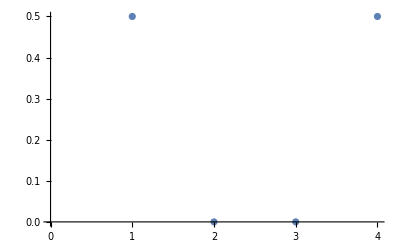

```mathematica
ListPlot[Table[Limit[test[[i]]/.{α->.00001,β->.00001}//FullSimplify,t->∞],{i,1,4}]]
```

```mathematica
testD = β/2*Limit[D[test,β],β->0]
```

$Aborted

```mathematica
blah = Gamma[θ1+θ2]/(Gamma[θ1]*Gamma[θ2])*x^(θ1-1)*(1-x)^(θ2-1)
```

((1-x)^(-1+θ2) x^(-1+θ1) Gamma[θ1+θ2])/(Gamma[θ1] Gamma[θ2])

```mathematica
blah2 = blah/.{θ2->θ,θ1->θ}
```

((1-x)^(-1+θ) x^(-1+θ) Gamma[2 θ])/Gamma[θ]^2

```mathematica
Limit[D[blah2,θ],θ->0]
```

1/(2 x-2 x^2)

```mathematica
Limit[blah+D[blah,θ1],θ1->0]
```

(1-x)^(-1+θ2)/x

```mathematica
MatrixExp[θ/2*Qmu*t].MatrixExp[Q*t]//FullSimplify//MatrixForm
```

(ⅇ^(-(3 t θ)/2) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^(2 t) (-3+4 ⅇ^t)) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^t)^2 (1+2 ⅇ^t) | 0
-ⅇ^(-(3 t θ)/2)+ⅇ^(-t θ) | 1/2 ⅇ^(-3/2 t (2+θ)) (1+ⅇ^(2 t) (3-4 ⅇ^t+2 ⅇ^((t θ)/2) (-1+2 ⅇ^t))) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^t) (1+ⅇ^t-2 ⅇ^(2 t)+2 ⅇ^(1/2 t (4+θ))) | 0
ⅇ^(-(3 t θ)/2) (-1+ⅇ^((t θ)/2))^2 | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^(2 t) (-3+4 (ⅇ^t+ⅇ^(t+t θ)+ⅇ^((t θ)/2) (1-2 ⅇ^t)))) | 1/2 ⅇ^(-3/2 t (2+θ)) (1+ⅇ^(2 t) (-3+2 (ⅇ^t+ⅇ^(t+t θ)-2 ⅇ^((t θ)/2) (-1+ⅇ^t)))) | 0
ⅇ^(-(3 t θ)/2) (-1+ⅇ^((t θ)/2))^3 | 1/2 ⅇ^(-3/2 t (2+θ)) (1+ⅇ^(2 t) (3-4 ⅇ^t-12 ⅇ^(t+t θ)+6 ⅇ^(t+(3 t θ)/2)+6 ⅇ^((t θ)/2) (-1+2 ⅇ^t))) | 1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^(2 t) (3-2 ⅇ^t-6 ⅇ^(t+t θ)+6 ⅇ^(t+(3 t θ)/2)+6 ⅇ^((t θ)/2) (-1+ⅇ^t))) | 1)

```mathematica
MatrixExp[Q*t].MatrixExp[θ/2*Qmu*t]//FullSimplify//MatrixForm
```

(1/2 ⅇ^(-3/2 t (2+θ)) (2-3 ⅇ^((t θ)/2)+ⅇ^(t θ)-3 ⅇ^(t (2+θ))+2 ⅇ^(t (3+θ))+3 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-t (3+θ)) (-3+3 ⅇ^(2 t)+2 ⅇ^((t θ)/2)-6 ⅇ^(1/2 t (4+θ))+4 ⅇ^(1/2 t (6+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (-1+ⅇ^t)^2 (1+2 ⅇ^t) | 0
1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^((t θ)/2)) (2+ⅇ^((t θ)/2) (-1+ⅇ^(2 t))) | -1/2 ⅇ^(-t (3+θ)) (-3+ⅇ^(2 t)+2 ⅇ^((t θ)/2)-2 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (-1+ⅇ^(2 t)) | 0
1/2 ⅇ^(-3/2 t (2+θ)) (-1+ⅇ^((t θ)/2)) (-2+ⅇ^((t θ)/2) (1+ⅇ^(2 t))) | -1/2 ⅇ^(-t (3+θ)) (3+ⅇ^(2 t)-2 ⅇ^((t θ)/2)-2 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (1+ⅇ^(2 t)) | 0
1/2 ⅇ^(-3/2 t (2+θ)) (-2+3 ⅇ^((t θ)/2)-ⅇ^(t θ)-3 ⅇ^(t (2+θ))+2 ⅇ^(3/2 t (2+θ))-2 ⅇ^(t (3+θ))+3 ⅇ^(1/2 t (4+θ))) | 1/2 ⅇ^(-t (3+θ)) (3+3 ⅇ^(2 t)-2 ⅇ^((t θ)/2)+6 ⅇ^(t (3+θ))-6 ⅇ^(1/2 t (4+θ))-4 ⅇ^(1/2 t (6+θ))) | 1/2 ⅇ^(-1/2 t (6+θ)) (-1+ⅇ^(2 t) (-3-2 ⅇ^t+6 ⅇ^(t+(t θ)/2))) | 1)

```mathematica
MatrixExp[θ/2*Qmu*t + Q*t]//FullSimplify //MatrixForm
```

((ⅇ^(-3/2 t (2+θ)) (θ (1+θ) (2+θ)+6 ⅇ^(1/2 t (4+θ)) θ (3+θ)+6 ⅇ^(t (3+θ)) (4+θ)))/((2+θ) (3+θ) (4+θ)) | (6 ⅇ^(-3/2 t (2+θ)) (-(1+θ) (2+θ)+2 ⅇ^(t (3+θ)) (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | (6 ⅇ^(-3/2 t (2+θ)) (2+θ-2 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) (4+θ)))/((2+θ) (3+θ) (4+θ)) | 0
(ⅇ^(-3/2 t (2+θ)) θ (-(1+θ) (2+θ)+2 ⅇ^(t (3+θ)) (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | (6 ⅇ^(-3/2 t (2+θ)) (1+θ))/((3+θ) (4+θ))+(4 ⅇ^(-(t θ)/2) θ)/(6+5 θ+θ^2)+(ⅇ^(-t (1+θ)) (-2+θ)^2)/(8+6 θ+θ^2) | -(2 ⅇ^(-3/2 t (2+θ)) (3 (2+θ)-ⅇ^(t (3+θ)) θ (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | 0
(ⅇ^(-3/2 t (2+θ)) θ (1+θ) (2+θ-2 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) (4+θ)))/((2+θ) (3+θ) (4+θ)) | -(2 ⅇ^(-3/2 t (2+θ)) (1+θ) (3 (2+θ)-ⅇ^(t (3+θ)) θ (4+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)))/((2+θ) (3+θ) (4+θ)) | (ⅇ^(-3/2 t (2+θ)) (6 (2+θ)+(1+θ) (4 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) θ (4+θ))))/((2+θ) (3+θ) (4+θ)) | 0
(1+θ) (2+θ) (-(ⅇ^(-3/2 t (2+θ)) θ)/((2+θ) (3+θ) (4+θ))+1/(2+3 θ+θ^2)-(3 ⅇ^(-(t θ)/2))/(6+5 θ+θ^2)+(3 ⅇ^(-t (1+θ)) θ)/(8+14 θ+7 θ^2+θ^3)) | (3 ⅇ^(-3/2 t (2+θ)) (2 (1+θ)+ⅇ^(1/2 t (4+θ)) (-6+θ+θ^2)+ⅇ^(t (3+θ)) (4+θ) (-2 (1+θ)+ⅇ^((t θ)/2) (3+θ))))/((3+θ) (4+θ)) | (ⅇ^(-t (4+3 θ)) (3 ⅇ^(t (4+3 θ)) (3+θ) (4+θ)-3 ⅇ^(t+(3 t θ)/2) (2+2 ⅇ^(1/2 t (4+θ)) (3+θ)+ⅇ^(t (3+θ)) (1+θ) (4+θ))))/((3+θ) (4+θ)) | 1)

```mathematica
o1 = θ/2*Integrate[MatrixExp[Q*s].Qmu.MatrixExp[Q*(t-s)],{s,0,t}]//FullSimplify
```

{{1/12 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t) θ,1/24 ⅇ^(-3 t) (-5+18 t-8 ⅇ^(3 t) (5+3 t)+9 ⅇ^(2 t) (5+4 t)) θ,-1/24 ⅇ^(-3 t) (7+18 t+4 ⅇ^(3 t) (5+3 t)-9 ⅇ^(2 t) (3+4 t)) θ,0},{1/12 (4-ⅇ^(-3 t)-3 ⅇ^-t) θ,1/24 ⅇ^(-3 t) (5+16 ⅇ^(3 t)-18 t-3 ⅇ^(2 t) (7+4 t)) θ,1/24 ⅇ^(-3 t) (7+8 ⅇ^(3 t)+18 t-3 ⅇ^(2 t) (5+4 t)) θ,0},{1/12 (2+ⅇ^(-3 t)-3 ⅇ^-t) θ,1/24 ⅇ^(-3 t) (-5+ⅇ^(2 t) (-3+8 ⅇ^t-12 t)+18 t) θ,1/24 ⅇ^(-3 t) (-7+ⅇ^(2 t) (3+4 ⅇ^t-12 t)-18 t) θ,0},{1/12 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t) θ,1/24 ⅇ^(-3 t) (5-18 t+8 ⅇ^(3 t) (-4+3 t)+9 ⅇ^(2 t) (3+4 t)) θ,1/24 ⅇ^(-3 t) (7+18 t+ⅇ^(2 t) (9+36 t+4 ⅇ^t (-4+3 t))) θ,0}}

```mathematica
test = (MatrixExp[Q*t]+o1).h1//FullSimplify
```

{1/24 ⅇ^(-3 t) (-1+x) (-2 θ+4 ⅇ^(3 t) (-6+(5+3 t) θ)+3 x (4+3 θ-6 t θ+4 x (-2+3 t θ))-9 ⅇ^(2 t) (2 θ+x (-4+θ+4 t θ))),1/24 ⅇ^(-3 t) (-1+x) (2 θ-8 ⅇ^(3 t) θ-3 x (4+(3-6 t) θ+4 x (-2+3 t θ))+3 ⅇ^(2 t) (2 θ+x (-4+(3+4 t) θ))),1/24 ⅇ^(-3 t) (-1+x) (-2 θ-4 ⅇ^(3 t) θ+3 x (4+(3-6 t) θ+4 x (-2+3 t θ))+3 ⅇ^(2 t) (2 θ+x (-4+(-3+4 t) θ))),1/24 ⅇ^(-3 t) (-4 ⅇ^(3 t) (-6 x+(-4+3 t) (-1+x) θ)-9 ⅇ^(2 t) (-1+x) (2 θ+x (-4+(-1+4 t) θ))-(-1+x) (-2 θ+3 x (4+(3-6 t) θ+4 x (-2+3 t θ))))}

```mathematica
Limit[test,t->∞]/.x->0
```

{θ (-∞),θ/3,θ/6,θ ∞}

```mathematica
Q = makeQ[5]
```

{{0,10,0,0,0,0},{0,-4,6,0,0,0},{0,1,-6,3,0,0},{0,0,3,-6,1,0},{0,0,0,6,-4,0},{0,0,0,0,10,0}}

```mathematica
p1 = MatrixExp[Q*t1]
```

{{1,1/14 ⅇ^(-10 t1) (-1-7 ⅇ^(4 t1)-20 ⅇ^(7 t1)-28 ⅇ^(9 t1)+56 ⅇ^(10 t1)),6+(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)-(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,4-(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)+(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,1/14 ⅇ^(-10 t1) (-1+ⅇ^t1)^4 (1+4 ⅇ^t1+10 ⅇ^(2 t1)+20 ⅇ^(3 t1)+28 ⅇ^(4 t1)+28 ⅇ^(5 t1)+14 ⅇ^(6 t1)),0},{0,1/70 ⅇ^(-10 t1) (5+21 ⅇ^(4 t1)+30 ⅇ^(7 t1)+14 ⅇ^(9 t1)),3/35 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),(3 ⅇ^(-10 t1))/7-(3 ⅇ^(-6 t1))/5-(3 ⅇ^(-3 t1))/7+(3 ⅇ^-t1)/5,1/70 ⅇ^(-10 t1) (-1+ⅇ^t1)^3 (5+15 ⅇ^t1+30 ⅇ^(2 t1)+50 ⅇ^(3 t1)+54 ⅇ^(4 t1)+42 ⅇ^(5 t1)+14 ⅇ^(6 t1)),0},{0,1/70 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (30+14 ⅇ^(4 t1)+5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (-30+14 ⅇ^(4 t1)-5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),ⅇ^(-10 t1)/14-ⅇ^(-6 t1)/10-ⅇ^(-3 t1)/14+ⅇ^-t1/10,0},{0,ⅇ^(-10 t1)/14-ⅇ^(-6 t1)/10-ⅇ^(-3 t1)/14+ⅇ^-t1/10,1/70 ⅇ^(-10 t1) (-30+14 ⅇ^(4 t1)-5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (30+14 ⅇ^(4 t1)+5 ⅇ^(7 t1)+21 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),0},{0,1/70 ⅇ^(-10 t1) (-1+ⅇ^t1)^3 (5+15 ⅇ^t1+30 ⅇ^(2 t1)+50 ⅇ^(3 t1)+54 ⅇ^(4 t1)+42 ⅇ^(5 t1)+14 ⅇ^(6 t1)),(3 ⅇ^(-10 t1))/7-(3 ⅇ^(-6 t1))/5-(3 ⅇ^(-3 t1))/7+(3 ⅇ^-t1)/5,3/35 ⅇ^(-10 t1) (-5-7 ⅇ^(4 t1)+5 ⅇ^(7 t1)+7 ⅇ^(9 t1)),1/70 ⅇ^(-10 t1) (5+21 ⅇ^(4 t1)+30 ⅇ^(7 t1)+14 ⅇ^(9 t1)),0},{0,1/14 ⅇ^(-10 t1) (-1+ⅇ^t1)^4 (1+4 ⅇ^t1+10 ⅇ^(2 t1)+20 ⅇ^(3 t1)+28 ⅇ^(4 t1)+28 ⅇ^(5 t1)+14 ⅇ^(6 t1)),4-(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)+(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,6+(3 ⅇ^(-10 t1))/7+ⅇ^(-6 t1)-(10 ⅇ^(-3 t1))/7-6 ⅇ^-t1,1/14 ⅇ^(-10 t1) (-1-7 ⅇ^(4 t1)-20 ⅇ^(7 t1)-28 ⅇ^(9 t1)+56 ⅇ^(10 t1)),1}}

```mathematica
p2 = MatrixExp[Q*t2]
```

{{1,1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)),1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2),0},{0,1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0},{0,1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),0},{0,1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2),1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)),1}}

```mathematica
{0,1,0,0}.p1
```

{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
{0,0,1,0}.p2
```

{0,1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),0}

```mathematica
h1=makeHet[5]
```

{(1-x)^5,(1-x)^4 x,(1-x)^3 x^2,(1-x)^2 x^3,(1-x) x^4,x^5}

```mathematica
test = p1.h1;
```

```mathematica
Integrate[test*x^-1*(1-x),{x,0,1}]//FullSimplify
```

Integrate::idiv: Integral of (ⅇ^(-10 t1) (-1+x)^2 (14 ⅇ^(10 t1)-28 ⅇ^(9 t1) x+20 ⅇ^(7 t1) x (-1+2 x)-7 ⅇ^(4 t1) x (1-5 x+5 x^2)+x (-1+9 x-21 x^2+14 x^3)))/(14 x) does not converge on {0,1}.

{∫_0^1 (ⅇ^(-10 t1) (-1+x)^2 (14 ⅇ^(10 t1)-28 ⅇ^(9 t1) x+20 ⅇ^(7 t1) x (-1+2 x)-7 ⅇ^(4 t1) x (1+5 (-1+x) x)+x (-1+2 x) (1+7 (-1+x) x)))/(14 x)ⅆx,1/840 ⅇ^(-10 t1) (3+21 ⅇ^(4 t1)+60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3-7 ⅇ^(4 t1)+10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (3-7 ⅇ^(4 t1)-10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3+21 ⅇ^(4 t1)-60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 (420+ⅇ^(-10 t1) (3-35 ⅇ^(4 t1)+200 ⅇ^(7 t1)-560 ⅇ^(9 t1)))}

```mathematica
co
```

```mathematica
init = Integrate[h1*x^-1*(1-x),{x,0,1}]
```

Integrate::idiv: Integral of (-1+x)^6/x does not converge on {0,1}.

{∫_0^1 (1-x)^6/x ⅆx,1/6,1/30,1/60,1/60,1/30}

```mathematica
p1.init//FullSimplify
```

{1/840 (798-ⅇ^(-10 t1) (3+35 ⅇ^(4 t1)+200 ⅇ^(7 t1)+560 ⅇ^(9 t1)))+∫_0^1 (-1+x)^6/x ⅆx,1/840 ⅇ^(-10 t1) (3+21 ⅇ^(4 t1)+60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3-7 ⅇ^(4 t1)+10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (3-7 ⅇ^(4 t1)-10 ⅇ^(7 t1)+28 ⅇ^(9 t1)),1/840 ⅇ^(-10 t1) (-3+21 ⅇ^(4 t1)-60 ⅇ^(7 t1)+56 ⅇ^(9 t1)),1/840 (420+ⅇ^(-10 t1) (3-35 ⅇ^(4 t1)+200 ⅇ^(7 t1)-560 ⅇ^(9 t1)))}

```mathematica
newMuts = o1.{1,0,0,0}
```

{1/12 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t) θ,1/12 (4-ⅇ^(-3 t)-3 ⅇ^-t) θ,1/12 (2+ⅇ^(-3 t)-3 ⅇ^-t) θ,1/12 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t) θ}

```mathematica
Integrate[MatrixExp[Qtest*s].Qmu.MatrixExp[Qtest*(t-s)].{1,0,0,0},{s,0,t}]
```

{1/6 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t),1/6 (4-ⅇ^(-3 t)-3 ⅇ^-t),1/6 (2+ⅇ^(-3 t)-3 ⅇ^-t),1/6 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t)}

```mathematica
MatrixExp[Qtest*(t-s)].{1,0,0,0}
```

{1,0,0,0}

```mathematica
Qmu.{1,0,0,0}
```

{-3,1,0,0}

```mathematica
makeQmu[6].{1,0,0,0,0,0,0}
```

{-6,1,0,0,0,0,0}

```mathematica
Integrate[Exp[a*s],{s,0,t}]
```

(-1+ⅇ^(a t))/a

```mathematica
Inverse[Qtest]
```

Inverse::sing: Matrix {{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}} is singular.

Inverse[{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}]

```mathematica
Integrate[MatrixExp[Qtest*s].{-3,1,0,0},{s,0,t}]
```

{1/6 (-10+ⅇ^(-3 t)+9 ⅇ^-t-6 t),1/6 (4-ⅇ^(-3 t)-3 ⅇ^-t),1/6 (2+ⅇ^(-3 t)-3 ⅇ^-t),1/6 (-8-ⅇ^(-3 t)+9 ⅇ^-t+6 t)}

```mathematica
Table[Binomial[3,i],{i,0,3}]*Limit[newMuts,t->∞]
```

{θ (-∞),θ,θ/2,θ ∞}

```mathematica
Qmu//MatrixForm
```

(-3 | 0 | 0 | 0
1 | -2 | 0 | 0
0 | 2 | -1 | 0
0 | 0 | 3 | 0)

```mathematica
projectMatrix[n_,m_]:=Table[Table[Binomial[l,i]*Binomial[n-l,m-i]/Binomial[n,m],{l,0,n}],{i,0,m}]
```

```mathematica
projectMatrix[6,5].Table[1,{i,1,5}]
```

{7/6,7/6,7/6,7/6}

```mathematica
Table[1/i,{i,1,5}]
```

{1,1/2,1/3,1/4,1/5}

```mathematica
projectMatrix[6,5]//MatrixForm
```

(5/6 | 1/3 | 0 | 0 | 0
0 | 2/3 | 1/2 | 0 | 0
0 | 0 | 1/2 | 2/3 | 0
0 | 0 | 0 | 1/3 | 5/6)

```mathematica
Q
```

{{0,10,0,0,0,0},{0,-4,6,0,0,0},{0,1,-6,3,0,0},{0,0,3,-6,1,0},{0,0,0,6,-4,0},{0,0,0,0,10,0}}

```mathematica
Q1 = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
Q2 = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
h1 = makeHet[3]
```

{(1-x)^3,(1-x)^2 x,(1-x) x^2,x^3}

```mathematica
h2 = makeHet[3]
```

{(1-x)^3,(1-x)^2 x,(1-x) x^2,x^3}

```mathematica
probForward = (MatrixExp[Q1*t1].h1)⊗(MatrixExp[Q2*t2].h2);
```

```mathematica
probForward[[2,2]]
```

(1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2) (1/10 ⅇ^(-6 t2) (2+5 ⅇ^(3 t2)+3 ⅇ^(5 t2)) (1-x)^3 x+3/5 ⅇ^(-6 t2) (-1+ⅇ^(5 t2)) (1-x)^2 x^2+1/10 ⅇ^(-6 t2) (-1+ⅇ^t2)^2 (2+4 ⅇ^t2+6 ⅇ^(2 t2)+3 ⅇ^(3 t2)) (1-x) x^3)

```mathematica
probBackward = (({1,0,0,0}.MatrixExp[Q1*t1].projectMatrix[4,3])*{1,0,0,0,0}.MatrixExp[Q2*t2])
```

{1,1/5 ⅇ^(-6 t2) (-1-5 ⅇ^(3 t2)-9 ⅇ^(5 t2)+15 ⅇ^(6 t2)) (1/4+3/8 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1))),(3+(3 ⅇ^(-6 t2))/5-(18 ⅇ^-t2)/5) (1/4 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1)+1/4 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1))),3/40 ⅇ^(-3 t1-6 t2) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (-1+ⅇ^t2)^3 (1+3 ⅇ^t2+6 ⅇ^(2 t2)+5 ⅇ^(3 t2)),0}

```mathematica
projectMatrix[4,3]//MatrixForm
```

(1 | 1/4 | 0 | 0 | 0
0 | 3/4 | 1/2 | 0 | 0
0 | 0 | 1/2 | 3/4 | 0
0 | 0 | 0 | 1/4 | 1)

```mathematica
{0,1,0,0}.projectMatrix[4,3]
```

{0,3/4,1/2,0,0}

```mathematica
Qd
```

{{0,6,0,0},{0,-3,3,0},{0,1,-4,1},{0,0,3,-3}}

```mathematica
Q = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
MatrixExp[Q*t2].MatrixExp[Q*t1].{0,1/1,1/2,0}//FullSimplify
```

{1/4 ⅇ^(-3 (t1+t2)) (-1+ⅇ^(2 (t1+t2)) (-9+10 ⅇ^(t1+t2))),1/4 ⅇ^(-3 (t1+t2)) (1+3 ⅇ^(2 (t1+t2))),1/4 ⅇ^(-3 (t1+t2)) (-1+3 ⅇ^(2 (t1+t2))),1/4 (8+ⅇ^(-3 (t1+t2)) (1-9 ⅇ^(2 (t1+t2))))}

```mathematica
{0,1/1,1/2,0}.(({0,1,0,0}.MatrixExp[Q1*t1])*({0,1,0,0}.MatrixExp[Q2*t2]))/.{t1->.5,t2->.5}//N
```

0.190459

```mathematica
{0,1/1,1/2,0}.(({0,1,0,0}.MatrixExp[Q1*t1])*({0,0,1,0}.MatrixExp[Q2*t2]))/.{t1->.5,t2->.5}//N
```

0.119285

```mathematica
neut = {0,1/1,1/2,0}/Table[Binomial[3,i],{i,0,3}]
```

{0,1/3,1/6,0}

```mathematica
bin = makeBinom[3,3]
```

{{1,3,3,1},{3,9,9,3},{3,9,9,3},{1,3,3,1}}

```mathematica
probForward = (MatrixExp[Q1*t1].neut)⊗(MatrixExp[Q2*t2].neut);
```

```mathematica
probForward[[2,2]]/.{t1->.25,t2->.25}//N
```

0.054786

```mathematica
Q1 = makeQ[2]
```

{{0,1,0},{0,-1,0},{0,1,0}}

```mathematica
Q2 = makeQ[2]
```

{{0,1,0},{0,-1,0},{0,1,0}}

```mathematica
neut = {0,1,0}
```

{0,1,0}

```mathematica
MatrixExp[Q1*t1].neut
```

{ⅇ^-t1 (-1+ⅇ^t1),ⅇ^-t1,ⅇ^-t1 (-1+ⅇ^t1)}

```mathematica
Exp[-t1]*Exp[-t2]/.{t1->.25,t2->.25}
```

0.606531

```mathematica
h = makeHet[2]
```

{(1-x)^2,(1-x) x,x^2}

```mathematica
probForward = (MatrixExp[Q1*t1].h)⊗(MatrixExp[Q2*t2].h);
```

```mathematica
probForward[[2,2]]
```

ⅇ^(-t1-t2) (1-x)^2 x^2

```mathematica
Integrate[probForward[[2,2]]*1/x,{x,0,1}]
```

ⅇ^(-t1-t2)/3

```mathematica
ⅇ^(-t1-t2)/3/.{t1->.5,t2->.5}
```

0.122626

```mathematica
h⊗h//MatrixForm
```

((1-x)^4 | (1-x)^3 x | (1-x)^2 x^2
(1-x)^3 x | (1-x)^2 x^2 | (1-x) x^3
(1-x)^2 x^2 | (1-x) x^3 | x^4)

```mathematica
h1⊗h//MatrixForm
```

((1-x)^5 | (1-x)^4 x | (1-x)^3 x^2
(1-x)^4 x | (1-x)^3 x^2 | (1-x)^2 x^3
(1-x)^3 x^2 | (1-x)^2 x^3 | (1-x) x^4
(1-x)^2 x^3 | (1-x) x^4 | x^5)

```mathematica
Q1 = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
Q2 = makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
({0,1,0,0}.MatrixExp[Q1*t1])⊗({0,0,1,0}.MatrixExp[Q2*t2])//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/4 ⅇ^(-3 t1-3 t2) (1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2)) | 1/4 ⅇ^(-3 t1-3 t2) (1+ⅇ^(2 t1)) (1+ⅇ^(2 t2)) | 0
0 | 1/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2)) | 1/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (1+ⅇ^(2 t2)) | 0
0 | 0 | 0 | 0)

```mathematica
Q = makeQ[2]
```

{{0,1,0},{0,-1,0},{0,1,0}}

```mathematica
({0,1,0}.MatrixExp[Q*t1])⊗({0,1,0}.MatrixExp[Q*t2])
```

```mathematica
h⊗h*{{0,0,0},{0,ⅇ^(-t1-t2),0},{0,0,0}}
```

{{0,0,0},{0,ⅇ^(-t1-t2) (1-x)^2 x^2,0},{0,0,0}}

```mathematica
({0,2,0}.MatrixExp[Q*t1].projectMatrix[4,2])*({0,2,0}.MatrixExp[Q*t2].projectMatrix[4,2])//FullSimplify
```

{0,ⅇ^(-t1-t2),(16 ⅇ^(-t1-t2))/9,ⅇ^(-t1-t2),0}

```mathematica
({0,1,0}.MatrixExp[Q*t1].projectMatrix[4,2])*({0,1,0}.MatrixExp[Q*t2].projectMatrix[4,2])//FullSimplify
```

{0,ⅇ^(-t1-t2)/4,(4 ⅇ^(-t1-t2))/9,ⅇ^(-t1-t2)/4,0}

```mathematica
{0,ⅇ^(-t1-t2)/4,(4 ⅇ^(-t1-t2))/9,ⅇ^(-t1-t2)/4,0}.{0,1/1,1/2,1/3,0}
```

(5 ⅇ^(-t1-t2))/9

```mathematica
h1⊗h1//MatrixForm
```

((1-x)^6 | (1-x)^5 x | (1-x)^4 x^2 | (1-x)^3 x^3
(1-x)^5 x | (1-x)^4 x^2 | (1-x)^3 x^3 | (1-x)^2 x^4
(1-x)^4 x^2 | (1-x)^3 x^3 | (1-x)^2 x^4 | (1-x) x^5
(1-x)^3 x^3 | (1-x)^2 x^4 | (1-x) x^5 | x^6)

```mathematica
{0,2,0}.MatrixExp[Q*t1]
```

{0,2 ⅇ^-t1,0}

```mathematica
{0,1,0,0}.MatrixExp[Q1*t1]
```

{0,1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
MatrixExp[Q1*t1].(Table[Binomial[3,i],{i,0,3}]*h1)//MatrixForm
```

((1-x)^3+3/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x)^2 x+3/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x) x^2
3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2
3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x)^2 x+3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x) x^2
3/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x)^2 x+3/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x) x^2+x^3)

```mathematica
(MatrixExp[Q1*t1].(h1))⊗(MatrixExp[Q1*t2].(h1))//MatrixForm
```

(((1-x)^3+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x) x^2) ((1-x)^3+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x) x^2) | ((1-x)^3+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x) x^2) (1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2) | ((1-x)^3+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x) x^2) (1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x) x^2) | ((1-x)^3+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x) x^2) (1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x) x^2+x^3)
(1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2) ((1-x)^3+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x) x^2) | (1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2) (1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2) | (1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2) (1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x) x^2) | (1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2) (1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x) x^2+x^3)
(1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x) x^2) ((1-x)^3+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x) x^2) | (1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x) x^2) (1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2) | (1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x) x^2) (1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x) x^2) | (1/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x)^2 x+1/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x) x^2) (1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x) x^2+x^3)
((1-x)^3+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x) x^2) (1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x) x^2+x^3) | (1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2) (1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x) x^2+x^3) | (1/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x)^2 x+1/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x) x^2) (1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x) x^2+x^3) | (1/2 ⅇ^(-3 t1) (-1+ⅇ^t1)^2 (1+2 ⅇ^t1) (1-x)^2 x+1/2 ⅇ^(-3 t1) (-1-3 ⅇ^(2 t1)+4 ⅇ^(3 t1)) (1-x) x^2+x^3) (1/2 ⅇ^(-3 t2) (-1+ⅇ^t2)^2 (1+2 ⅇ^t2) (1-x)^2 x+1/2 ⅇ^(-3 t2) (-1-3 ⅇ^(2 t2)+4 ⅇ^(3 t2)) (1-x) x^2+x^3))

```mathematica
((MatrixExp[Q1*t1].(Table[Binomial[3,k],{k,0,3}]*h1))⊗(MatrixExp[Q1*t2].(Table[Binomial[3,k],{k,0,3}]*h1)))[[2,2]]
```

(3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2) (3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x+3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2)

```mathematica
Integrate[%*1/x,{x,0,1}]
```

```mathematica
3/80 ⅇ^(-3 (t1+t2)) (1+ⅇ^(2 t1)+ⅇ^(2 t2)+5 ⅇ^(2 (t1+t2)))/.{t1->.34,t2->.34/3.5}
```

0.16342

```mathematica
p1 = {0,3,0,0}.MatrixExp[Q1*t1]
```

{0,3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
p2 = {0,3,0,0}.MatrixExp[Q1*t2]
```

{0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0}

```mathematica
p1[[2]]*p2[[3]]*1/(3*Binomial[6,3])//FullSimplify
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t1] Sinh[t2]

```mathematica
p1[[3]]*p2[[2]]*1/(3*Binomial[6,3])//FullSimplify
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t2] Sinh[t1]

```mathematica
p1[[2]]*p2[[2]]*(1/(2*Binomial[6,2]))//FullSimplify
```

3/10 ⅇ^(-2 (t1+t2)) Cosh[t1] Cosh[t2]

```mathematica
p1[[3]]*p1[[3]]*1/(4*Binomial[6,4])//FullSimplify
```

3/80 ⅇ^(-6 t1) (-1+ⅇ^(2 t1))^2

```mathematica
p1[[2]]*p2[[3]]*1/(3*Binomial[6,3])+p1[[3]]*p2[[2]]*1/(3*Binomial[6,3])+p1[[2]]*p2[[2]]*(1/(2*Binomial[6,2]))+p1[[3]]*p1[[3]]*1/(4*Binomial[6,4])//FullSimplify
```

1/80 ⅇ^(-3 (2 t1+t2)) (6 ⅇ^(5 t1)+3 ⅇ^(3 t2) (-1+ⅇ^(2 t1))^2+6 ⅇ^(3 t1+2 t2) (1+2 ⅇ^(2 t1)))

```mathematica
Integrate[(3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2)*(3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x)*1/x,{x,0,1}]
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t2] Sinh[t1]

```mathematica
Integrate[p1[[3]]*p2[[2]]*x^3*(1-x)^3*1/x,{x,0,1}]//FullSimplify
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t2] Sinh[t1]

```mathematica
?Expand
```

Expand[expr] expands out products and positive integer powers in expr. 
Expand[expr,patt] leaves unexpanded any parts of expr that are free of the pattern patt.

```mathematica
Integrate[(3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x+3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2) (3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x+3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2)*1/x,{x,0,1}]//FullSimplify
```

```mathematica
3/80 ⅇ^(-3 (t1+t2)) (1+ⅇ^(2 t1)+ⅇ^(2 t2)+5 ⅇ^(2 (t1+t2)))/.{t1->.34,t2->.34/2}//N
```

0.148149

```mathematica
p1[[2]]*p2[[3]]*1/(3*Binomial[6,3])+p1[[3]]*p2[[2]]*1/(3*Binomial[6,3])+p1[[2]]*p2[[2]]*(1/(2*Binomial[6,2]))+p1[[3]]*p2[[3]]*1/(4*Binomial[6,4])//FullSimplify
```

```mathematica
3/80 ⅇ^(-3 (t1+t2)) (1+ⅇ^(2 t1)+ⅇ^(2 t2)+5 ⅇ^(2 (t1+t2)))/.{t1->.34,t2->.34/2}//N
```

0.148149

```mathematica
Integrate[(3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x)*(3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2)*1/x,{x,0,1}]
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t1] Sinh[t2]

```mathematica
p1[[2]]*p2[[3]]*1/(3*Binomial[6,3])//FullSimplify
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t1] Sinh[t2]

```mathematica
Integrate[(3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2)*(3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x)*1/x,{x,0,1}]//FullSimplify
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t2] Sinh[t1]

```mathematica
p1[[3]]*p2[[2]]*1/(3*Binomial[6,3])//FullSimplify
```

3/20 ⅇ^(-2 (t1+t2)) Cosh[t2] Sinh[t1]

```mathematica
Integrate[(3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) (1-x)^2 x)*(3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)) (1-x)^2 x)*1/x,{x,0,1}]//FullSimplify
```

3/10 ⅇ^(-2 (t1+t2)) Cosh[t1] Cosh[t2]

```mathematica
p1[[2]]*p2[[2]]*(1/(2*Binomial[6,2]))//FullSimplify
```

3/10 ⅇ^(-2 (t1+t2)) Cosh[t1] Cosh[t2]

```mathematica
Integrate[(3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) (1-x) x^2)*(3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)) (1-x) x^2)*1/x,{x,0,1}]
```

3/20 ⅇ^(-2 (t1+t2)) Sinh[t1] Sinh[t2]

```mathematica
p1[[3]]*p2[[3]]*1/(4*Binomial[6,4])//FullSimplify
```

3/20 ⅇ^(-2 (t1+t2)) Sinh[t1] Sinh[t2]

```mathematica
Table[Sum[p1[[k+1]]*p2[[j-k+1]],{k,1,3}],{j,0,6}]//MatrixForm
```

Part::partw: Part 5 of {0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0} does not exist.

Part::partw: Part 6 of {0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0} does not exist.

Part::partw: Part 5 of {0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) List
3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) List
9/4 ⅇ^(-3 t1-3 t2) (1+ⅇ^(2 t1)) (1+ⅇ^(2 t2))
9/4 ⅇ^(-3 t1-3 t2) (1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))+9/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (1+ⅇ^(2 t2))
9/4 ⅇ^(-3 t1-3 t2) (-1+ⅇ^(2 t1)) (-1+ⅇ^(2 t2))
3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) {0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0}⟦5⟧
3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)) {0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0}⟦5⟧+3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)) {0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0}⟦6⟧)

```mathematica
p1
```

{0,3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
p2
```

{0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0}

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
makeA[k_,n1_,n2_]:=Table[Table[If[i+j==k,1,0],{i,0,n1}],{j,0,n2}]
```

```mathematica
A = makeA[6,3,3]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}

```mathematica
p1
```

{0,3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1)),0}

```mathematica
p2
```

{0,3/2 ⅇ^(-3 t2) (1+ⅇ^(2 t2)),3/2 ⅇ^(-3 t2) (-1+ⅇ^(2 t2)),0}

```mathematica
p1.A.p2
```

0

```mathematica
p1[[2;;1]]
```

{}

```mathematica
p1[[1;;3]]
```

{0,3/2 ⅇ^(-3 t1) (1+ⅇ^(2 t1)),3/2 ⅇ^(-3 t1) (-1+ⅇ^(2 t1))}

```mathematica
Sinh[0]
```

0

```mathematica
?BesselK
```

BesselK[n,z] gives the modified Bessel function of the second kind K_n(z).

```mathematica
{1,0,0,0}.MatrixExp[Q1*s]//FullSimplify
```

```mathematica
{1,2-1/2 ⅇ^(-3 s) (1+3 ⅇ^(2 s)),1/2 (2+ⅇ^(-3 s)-3 ⅇ^-s),0}.makeAmu[3]
```

-1-1/2 ⅇ^(-3 s) (1+3 ⅇ^(2 s))

```mathematica
makeQmu[3].MatrixExp[makeQ[3]*t]
```

{{-3,-3/2 ⅇ^(-3 t) (-1-3 ⅇ^(2 t)+4 ⅇ^(3 t)),-3/2 ⅇ^(-3 t) (-1+ⅇ^t)^2 (1+2 ⅇ^t),0},{1,-ⅇ^(-3 t) (1+ⅇ^(2 t))+1/2 ⅇ^(-3 t) (-1-3 ⅇ^(2 t)+4 ⅇ^(3 t)),1/2 ⅇ^(-3 t) (-1+ⅇ^t)^2 (1+2 ⅇ^t)-ⅇ^(-3 t) (-1+ⅇ^(2 t)),0},{0,-1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t))+ⅇ^(-3 t) (1+ⅇ^(2 t)),ⅇ^(-3 t) (-1+ⅇ^(2 t))-1/2 ⅇ^(-3 t) (1+ⅇ^(2 t)),0},{0,3/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)),3/2 ⅇ^(-3 t) (1+ⅇ^(2 t)),0}}

```mathematica
makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
makeQmu[3].{1,0,0,0}
```

{-3,1,0,0}

```mathematica
MatrixExp[makeQ[3]*t].{1,0,0,0}
```

{1,0,0,0}

```mathematica
makeQ[3]
```

{{0,3,0,0},{0,-2,1,0},{0,1,-2,0},{0,0,3,0}}

```mathematica
makeQ[10][[2;;10,2;;10]]
```

{{-4,6,0,0},{1,-6,3,0},{0,3,-6,1},{0,0,6,-4}}

```mathematica
makeQ[5]
```

{{0,10,0,0,0,0},{0,-4,6,0,0,0},{0,1,-6,3,0,0},{0,0,3,-6,1,0},{0,0,0,6,-4,0},{0,0,0,0,10,0}}

```mathematica
qSub = makeQ[5][[2;;5,2;;5]];
```

```mathematica
blah = Table[Table[Binomial[5,k],{k,1,4}]*Inverse[qSub].(MatrixExp[qSub*T]-IdentityMatrix[4]).{1,0,0,0}/.T->x//N,{x,0,10,.01}];
```

```mathematica
blah/Total[blah]
```

{0.705098,0.201543,0.069897,0.023462}

```mathematica
Table[Binomial[5,k],{k,0,5}]*(NIntegrate[MatrixExp[makeQ[5]*(t-s)].makeQmu[5].MatrixExp[makeQ[5]*s].{1,0,0,0,0,0},{s,0,t}]/.t->.5)
```

NIntegrate::nlim: s = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{-1.74316,1.2214,0.349122,0.121079,0.0406419,0.0109097}

```mathematica
makeQmu[6].{1,0,0,0,0,0,0}
```

{-6,1,0,0,0,0,0}

```mathematica
stuff = Table[1/k,{k,1,9}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9}

```mathematica
stuff/Total[stuff]//N
```

{0.353486,0.176743,0.117829,0.0883714,0.0706972,0.0589143,0.050498,0.0441857,0.0392762}

```mathematica
blah = MatrixExp[makeQ[3]*t].makeHet[3];
```

```mathematica
Total[blah]
```

(1-x)^3+1/2 ⅇ^(-3 t) (-1+ⅇ^t)^2 (1+2 ⅇ^t) (1-x)^2 x+1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (1-x)^2 x+1/2 ⅇ^(-3 t) (1+ⅇ^(2 t)) (1-x)^2 x+1/2 ⅇ^(-3 t) (-1-3 ⅇ^(2 t)+4 ⅇ^(3 t)) (1-x)^2 x+1/2 ⅇ^(-3 t) (-1+ⅇ^t)^2 (1+2 ⅇ^t) (1-x) x^2+1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (1-x) x^2+1/2 ⅇ^(-3 t) (1+ⅇ^(2 t)) (1-x) x^2+1/2 ⅇ^(-3 t) (-1-3 ⅇ^(2 t)+4 ⅇ^(3 t)) (1-x) x^2+x^3

```mathematica
Limit[blah/Total[blah],x->0]
```

{1,0,0,0}

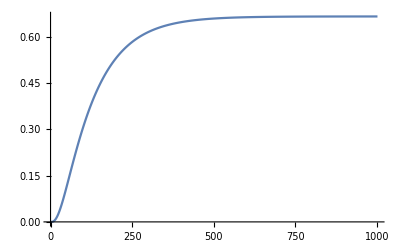

```mathematica
ListLinePlot[blah[[;;,3]]]
```

```mathematica
Limit[D[makeHet[3],x],x->0]
```

{-3,1,0,0}

```mathematica
1/2*MatrixExp[makeQ[5]*t].{-5,1,0,0,0,0}/.t->.2//N
```

{-1.79087,0.249488,0.0406438,0.0111098,0.00461631,0.00281241}

```mathematica
makeQmu[5].{1,0,0,0,0,0}
```

{-5,1,0,0,0,0}

```mathematica
blah = {0.24948810351608466,0.04064383966033948,0.011109814456238508,0.004616310673172384}
```

{0.249488,0.0406438,0.0111098,0.00461631}

```mathematica
blah/Total[blah]
```

{0.815699,0.132885,0.0363234,0.015093}

```mathematica
Limit[D[x/β^2*(α^2*Exp[α*t])/(Exp[α*t]-1)^2*Exp[(-α*(x*Exp[α*t]+y))/(β*(Exp[α*t]-1))]*Sum[1/(n!*(n+1)!)*((α*(x*y*Exp[α*t])^(1/2))/(β*(Exp[α*t]-1)))^(2*n),n,0,∞],x],x->0]
```

$Aborted

```mathematica
Limit[D[MatrixExp[makeQ[3]*t].makeHet[3],x],x->0]/.t->.2//N
```

{-2.5025,0.683771,0.13496,0.0463097}

```mathematica
MatrixExp[makeQ[5]*t].makeHet[5]/.x->.0001/.t->.2//N
```

{0.999642,0.0000498825,8.12955×10^-6,2.22316×10^-6,9.24226×10^-7,5.63405×10^-7}

```mathematica
blah = Table[Binomial[5,k],{k,1,5}]*{0.000049882540579612664,8.129546509498517*^-6,2.223160580495569*^-6,9.242261506725088*^-7,5.634052967298558*^-7}
```

{0.000249413,0.0000812955,0.0000222316,4.62113×10^-6,5.63405×10^-7}

```mathematica
blah/Total[blah]
```

{0.696442,0.227003,0.0620779,0.0129037,0.00157321}

```mathematica
a = Table[Binomial[5,k],{k,0,5}]*MatrixExp[makeQ[5]*t].{5,1,0,0,0,0}/.t->.5//N
```

{7.44281,1.16175,0.711309,0.402178,0.200669,0.0812838}

```mathematica
b = MatrixExp[makeQ[5]*t].makeHet[5]/.x->.0001/.t->.2//N
```

{0.999642,0.0000498825,8.12955×10^-6,2.22316×10^-6,9.24226×10^-7,5.63405×10^-7}

```mathematica
a/Total[a]
```

{0.744281,0.116175,0.0711309,0.0402178,0.0200669,0.00812838}

```mathematica
Inverse[makeQ[5][[2;;5,2;;5]]]
```

{{-2/5,-3/5,-2/5,-1/10},{-1/10,-2/5,-4/15,-1/15},{-1/15,-4/15,-2/5,-1/10},{-1/10,-2/5,-3/5,-2/5}}

```mathematica
PseudoInverse[makeQ[5]]
```

{{0,0,0,0,0,0},{121/1260,-4/315,-1/90,1/315,11/1260,1/315},{3/70,37/420,-8/105,1/210,3/70,1/60},{1/60,3/70,1/210,-8/105,37/420,3/70},{1/315,11/1260,1/315,-1/90,-4/315,121/1260},{0,0,0,0,0,0}}

```mathematica
b[[2;;5]]/Total[b[[2;;5]]]
```

{0.815614,0.132924,0.0363502,0.0151117}

```mathematica
Total[a[[2;;6]]]
```

3.58174

```mathematica
blah = Table[Binomial[5,k],{k,1,4}]*Inverse[qSub].(MatrixExp[qSub*T]-IdentityMatrix[4]).{1,0,0,0}/.T->.2//N
```

{0.709129,0.110466,0.0191376,0.00281241}

```mathematica
blah/Total[blah]
```

{0.842652,0.131265,0.022741,0.00334196}

```mathematica
blah2 = Table[Binomial[5,k],{k,0,5}]*PseudoInverse[makeQ[5]].(MatrixExp[makeQ[5]*T]-IdentityMatrix[6]).{-5,1,0,0,0,0}/.T->.2//N
```

{0.,0.709129,0.110466,0.0191376,0.00281241,0.}

```mathematica
MatrixExp[makeQ[1]*t].{-1,1}
```

{-1,1}

```mathematica
L[x]
```

0

```mathematica
D[makeHet[1],x]/.x->0
```

{-1,1}

```mathematica
makeInject[5]
```

{-5,1,0,0,0,0}

```mathematica
c = Table[(MatrixExp[makeQ[n]*.2].makeInject[n])[[n+1]],{n,1,5}]
```

{1.,0.181269,0.0463097,0.0148574,0.00562482}

```mathematica
makeInject[n_]:=Table[Piecewise[{{-n,k==0},{1,k==1}}],{k,0,n}]
```

```mathematica
a = Table[Binomial[5,k],{k,0,5}]*MatrixExp[makeQ[5]*t].makeInject[5]/.t->.732//N
Total[a[[2;;5]]]
```

{MatrixExp[0.732 makeQ[5.]].{-5.,1.,0.,0.,0.,0.},5. MatrixExp[0.732 makeQ[5.]].{-5.,1.,0.,0.,0.,0.},10. MatrixExp[0.732 makeQ[5.]].{-5.,1.,0.,0.,0.,0.},10. MatrixExp[0.732 makeQ[5.]].{-5.,1.,0.,0.,0.,0.},5. MatrixExp[0.732 makeQ[5.]].{-5.,1.,0.,0.,0.,0.},MatrixExp[0.732 makeQ[5.]].{-5.,1.,0.,0.,0.,0.}}

30. MatrixExp[0.732 makeQ[5.]].{-5.,1.,0.,0.,0.,0.}

```mathematica
Table[Binomial[5,k],{k,0,5}]*MatrixExp[makeQ[5]*t].makeHet[5]/.x->.2/.t->10//N
```

{0.799985,7.26399×10^-6,7.26399×10^-6,7.26399×10^-6,7.26399×10^-6,0.199985}

```mathematica
makeQsub[n_]:=makeQ[n][[2;;n,2;;n]]
```

```mathematica
makeQsub[5]
```

{{-4,6,0,0},{1,-6,3,0},{0,3,-6,1},{0,0,6,-4}}

```mathematica
makeIntegrated[n_,t_]:=Inverse[makeQsub[n]].(MatrixExp[makeQsub[n]*t]-IdentityMatrix[n-1])
```

```mathematica
θ/2*Table[Binomial[5,k],{k,1,4}]*Limit[makeIntegrated[5,t],t->∞]
```

{θ,θ/2,θ/3,θ/4}

```mathematica
blah = Table[Binomial[5,k],{k,1,4}]*(MatrixExp[makeQsub[5]*t].Table[θ/k/Binomial[5,k],{k,1,4}]+θ/2*makeIntegrated[5,t])//FullSimplify
```

{θ,θ/2,θ/3,θ/4}

```mathematica
θ/k/Binomial[n,k]//FullSimplify
```

θ/(k Binomial[n,k])

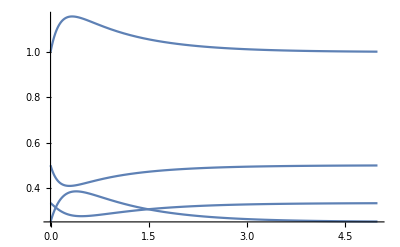

```mathematica
Plot[blah/.θ->1,{t,0,5}]
```

```mathematica
blah/.t->0
```

{5 θ,5 θ,(10 θ)/3,(5 θ)/4}

```mathematica
stuff = Table[Binomial[5,k],{k,1,4}]*θ/2*makeIntegrated[5,t];
```

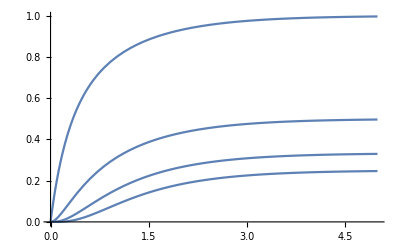

```mathematica
Plot[stuff/.θ->1,{t,0,5}]
```

```mathematica
things = Table[Binomial[5,k],{k,1,4}]*MatrixExp[makeQsub[5]*t].Table[θ/k/Binomial[5,k],{k,1,4}];
```

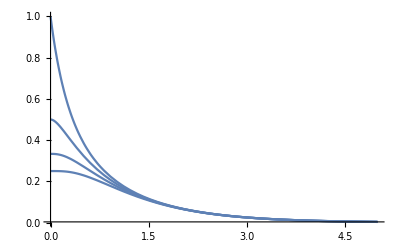

```mathematica
Plot[things/.θ->1,{t,0,5},PlotRange->All]
```

```mathematica
a ={0,0,0,0,1,0}.MatrixExp[makeQ[5]*t2]
```

{0,1/70 ⅇ^(-10 t2) (-1+ⅇ^t2)^3 (5+15 ⅇ^t2+30 ⅇ^(2 t2)+50 ⅇ^(3 t2)+54 ⅇ^(4 t2)+42 ⅇ^(5 t2)+14 ⅇ^(6 t2)),(3 ⅇ^(-10 t2))/7-(3 ⅇ^(-6 t2))/5-(3 ⅇ^(-3 t2))/7+(3 ⅇ^-t2)/5,3/35 ⅇ^(-10 t2) (-5-7 ⅇ^(4 t2)+5 ⅇ^(7 t2)+7 ⅇ^(9 t2)),1/70 ⅇ^(-10 t2) (5+21 ⅇ^(4 t2)+30 ⅇ^(7 t2)+14 ⅇ^(9 t2)),0}

```mathematica
b = MatrixExp[makeQ[10]*t1].makeInject[10]
```

{-10+(ⅇ^(-45 t1) (-1-17 ⅇ^(9 t1)-135 ⅇ^(17 t1)-663 ⅇ^(24 t1)-2244 ⅇ^(30 t1)-5508 ⅇ^(35 t1)-9996 ⅇ^(39 t1)-13260 ⅇ^(42 t1)-11934 ⅇ^(44 t1)+43758 ⅇ^(45 t1)))/4862,(ⅇ^(-45 t1) (5+68 ⅇ^(9 t1)+420 ⅇ^(17 t1)+1547 ⅇ^(24 t1)+3740 ⅇ^(30 t1)+6120 ⅇ^(35 t1)+6664 ⅇ^(39 t1)+4420 ⅇ^(42 t1)+1326 ⅇ^(44 t1)))/24310,(ⅇ^(-45 t1) (-15-153 ⅇ^(9 t1)-665 ⅇ^(17 t1)-1547 ⅇ^(24 t1)-1870 ⅇ^(30 t1)-510 ⅇ^(35 t1)+1666 ⅇ^(39 t1)+2210 ⅇ^(42 t1)+884 ⅇ^(44 t1)))/72930,(ⅇ^(-45 t1) (30+204 ⅇ^(9 t1)+480 ⅇ^(17 t1)+221 ⅇ^(24 t1)-935 ⅇ^(30 t1)-1530 ⅇ^(35 t1)-238 ⅇ^(39 t1)+1105 ⅇ^(42 t1)+663 ⅇ^(44 t1)))/145860,(ⅇ^(-45 t1) (-105-357 ⅇ^(9 t1)+105 ⅇ^(17 t1)+1547 ⅇ^(24 t1)+935 ⅇ^(30 t1)-2295 ⅇ^(35 t1)-2261 ⅇ^(39 t1)+1105 ⅇ^(42 t1)+1326 ⅇ^(44 t1)))/510510,(ⅇ^(-45 t1) (21-140 ⅇ^(17 t1)+374 ⅇ^(30 t1)-476 ⅇ^(39 t1)+221 ⅇ^(44 t1)))/102102,(ⅇ^(-45 t1) (-105+357 ⅇ^(9 t1)+105 ⅇ^(17 t1)-1547 ⅇ^(24 t1)+935 ⅇ^(30 t1)+2295 ⅇ^(35 t1)-2261 ⅇ^(39 t1)-1105 ⅇ^(42 t1)+1326 ⅇ^(44 t1)))/510510,(ⅇ^(-45 t1) (30-204 ⅇ^(9 t1)+480 ⅇ^(17 t1)-221 ⅇ^(24 t1)-935 ⅇ^(30 t1)+1530 ⅇ^(35 t1)-238 ⅇ^(39 t1)-1105 ⅇ^(42 t1)+663 ⅇ^(44 t1)))/145860,(ⅇ^(-45 t1) (-15+153 ⅇ^(9 t1)-665 ⅇ^(17 t1)+1547 ⅇ^(24 t1)-1870 ⅇ^(30 t1)+510 ⅇ^(35 t1)+1666 ⅇ^(39 t1)-2210 ⅇ^(42 t1)+884 ⅇ^(44 t1)))/72930,(ⅇ^(-45 t1) (5-68 ⅇ^(9 t1)+420 ⅇ^(17 t1)-1547 ⅇ^(24 t1)+3740 ⅇ^(30 t1)-6120 ⅇ^(35 t1)+6664 ⅇ^(39 t1)-4420 ⅇ^(42 t1)+1326 ⅇ^(44 t1)))/24310,(ⅇ^(-45 t1) (-1+17 ⅇ^(9 t1)-135 ⅇ^(17 t1)+663 ⅇ^(24 t1)-2244 ⅇ^(30 t1)+5508 ⅇ^(35 t1)-9996 ⅇ^(39 t1)+13260 ⅇ^(42 t1)-11934 ⅇ^(44 t1)+4862 ⅇ^(45 t1)))/4862}

```mathematica
like = Join[a,{0,0,0,0,0}].b;
```

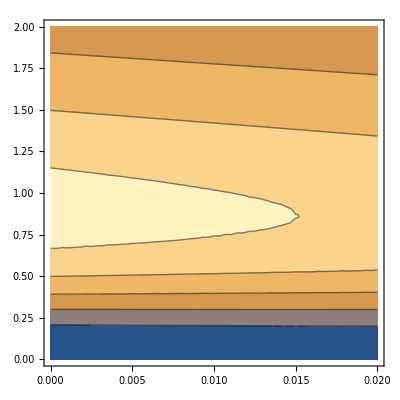

```mathematica
ContourPlot[like,{t1,0,.02},{t2,0,2}]
```

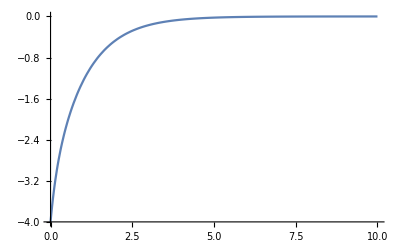

```mathematica
Plot[Total[MatrixExp[makeQ[5]*t].makeInject[5]],{t,0,10},PlotRange->All]
```

```mathematica
MatrixExp[makeQ[5]*t].makeInject[5]/.t->100//N
```

{-1.,7.44015195204167×10^-45,3.72007597602084×10^-45,3.72008×10^-45,7.44015195204167×10^-45,1.}

```mathematica
makeInject[5]
```

{-5,1,0,0,0,0}

```mathematica
makeIntegrated[4,t]
```

{1/2 (1-ⅇ^(-6 t)/5-ⅇ^(-3 t)/2-(3 ⅇ^-t)/10)+1/6 (-1/5 ⅇ^(-6 t)+ⅇ^(-3 t)/2-(3 ⅇ^-t)/10)+1/2 (ⅇ^(-6 t)/5-ⅇ^-t/5),1/6 (1-ⅇ^(-6 t)/5-ⅇ^(-3 t)/2-(3 ⅇ^-t)/10)+1/6 (-1/5 ⅇ^(-6 t)+ⅇ^(-3 t)/2-(3 ⅇ^-t)/10)+1/2 (ⅇ^(-6 t)/5-ⅇ^-t/5),1/6 (1-ⅇ^(-6 t)/5-ⅇ^(-3 t)/2-(3 ⅇ^-t)/10)+1/2 (-1/5 ⅇ^(-6 t)+ⅇ^(-3 t)/2-(3 ⅇ^-t)/10)+1/2 (ⅇ^(-6 t)/5-ⅇ^-t/5)}

```mathematica
a = Inverse[makeQsub[5]]
```

{{-2/5,-3/5,-2/5,-1/10},{-1/10,-2/5,-4/15,-1/15},{-1/15,-4/15,-2/5,-1/10},{-1/10,-2/5,-3/5,-2/5}}

```mathematica
b = MatrixExp[makeQsub[5]*t]-IdentityMatrix[5-1]
```

{{-1+ⅇ^(-10 t)/14+(3 ⅇ^(-6 t))/10+(3 ⅇ^(-3 t))/7+ⅇ^-t/5,-3/7 ⅇ^(-10 t)-(3 ⅇ^(-6 t))/5+(3 ⅇ^(-3 t))/7+(3 ⅇ^-t)/5,(3 ⅇ^(-10 t))/7-(3 ⅇ^(-6 t))/5-(3 ⅇ^(-3 t))/7+(3 ⅇ^-t)/5,-1/14 ⅇ^(-10 t)+(3 ⅇ^(-6 t))/10-(3 ⅇ^(-3 t))/7+ⅇ^-t/5},{-1/14 ⅇ^(-10 t)-ⅇ^(-6 t)/10+ⅇ^(-3 t)/14+ⅇ^-t/10,-1+(3 ⅇ^(-10 t))/7+ⅇ^(-6 t)/5+ⅇ^(-3 t)/14+(3 ⅇ^-t)/10,-3/7 ⅇ^(-10 t)+ⅇ^(-6 t)/5-ⅇ^(-3 t)/14+(3 ⅇ^-t)/10,ⅇ^(-10 t)/14-ⅇ^(-6 t)/10-ⅇ^(-3 t)/14+ⅇ^-t/10},{ⅇ^(-10 t)/14-ⅇ^(-6 t)/10-ⅇ^(-3 t)/14+ⅇ^-t/10,-3/7 ⅇ^(-10 t)+ⅇ^(-6 t)/5-ⅇ^(-3 t)/14+(3 ⅇ^-t)/10,-1+(3 ⅇ^(-10 t))/7+ⅇ^(-6 t)/5+ⅇ^(-3 t)/14+(3 ⅇ^-t)/10,-1/14 ⅇ^(-10 t)-ⅇ^(-6 t)/10+ⅇ^(-3 t)/14+ⅇ^-t/10},{-1/14 ⅇ^(-10 t)+(3 ⅇ^(-6 t))/10-(3 ⅇ^(-3 t))/7+ⅇ^-t/5,(3 ⅇ^(-10 t))/7-(3 ⅇ^(-6 t))/5-(3 ⅇ^(-3 t))/7+(3 ⅇ^-t)/5,-3/7 ⅇ^(-10 t)-(3 ⅇ^(-6 t))/5+(3 ⅇ^(-3 t))/7+(3 ⅇ^-t)/5,-1+ⅇ^(-10 t)/14+(3 ⅇ^(-6 t))/10+(3 ⅇ^(-3 t))/7+ⅇ^-t/5}}

```mathematica
a.b/.t->.2
```

{{0.141826,0.0662794,0.0114825,0.000562482},{0.0110466,0.125474,0.0298747,0.00191376},{0.00191376,0.0298747,0.125474,0.0110466},{0.000562482,0.0114825,0.0662794,0.141826}}

```mathematica
makeIntegrated[5,.2]
```

{{0.141826,0.0662794,0.0114825,0.000562482},{0.0110466,0.125474,0.0298747,0.00191376},{0.00191376,0.0298747,0.125474,0.0110466},{0.000562482,0.0114825,0.0662794,0.141826}}

```mathematica
Integrate[Exp[-r*s],{s,0,t}]
```

(1-ⅇ^(-r t))/r

```mathematica
[u==(1-ⅇ^(-r t))/r,t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[1/(1-r u)])/r,C[1]∈Integers]}}

```mathematica
Log[1/(1-r*u)]/r/.r->2/.u->1
```

(ⅈ π)/2

1/2 Log[1/(1-2 u)]

```mathematica
Exp[r*Log[1/(1-r*u)]/r]
```

1/(1-r u)

```mathematica
Integrate[1/(1-r*u)^2 Exp[q*u],{u,0,t}]
```

ConditionalExpression[-(r+ⅇ^(q/r) q ExpIntegralEi[-q/r])/r^2-(ⅇ^(q/r) (ⅇ^(q (-1/r+t)) r+(q-q r t) ExpIntegralEi[q (-1/r+t)]))/(r^2 (-1+r t)),((Im[r] Re[q]≥Im[q] Re[r]&&(Im[q]^2+Re[q]^2) (Im[t] Re[r]+Im[r] Re[t])≥0)||(Im[t] Re[q]+Im[q] Re[t]≥0&&((Im[q]^2+Re[q]^2) (Im[t] Re[r]+Im[r] Re[t])≤0||Im[r] Re[q]+Im[r]^2 (Im[t] Re[q]+Im[q] Re[t])+Re[r]^2 (Im[t] Re[q]+Im[q] Re[t])≤Im[q] Re[r]))||(Im[t] Re[q]+Im[q] Re[t]≤0&&(Im[r] Re[q]≤Im[q] Re[r]||Im[r] Re[q]+Im[r]^2 (Im[t] Re[q]+Im[q] Re[t])+Re[r]^2 (Im[t] Re[q]+Im[q] Re[t])≥Im[q] Re[r])))&&(1/(r t)∉Reals||Re[1/(r t)]>1||Re[1/(r t)]<0)]

```mathematica
Series[1/(1-r*u)^2,{r,0,2}]
```

1+2 u r+3 u^2 r^2+O[r]^3

```mathematica
FullSimplify[-(r+ⅇ^(q/r) q ExpIntegralEi[-q/r])/r^2-(ⅇ^(q/r) (ⅇ^(q (-1/r+t)) r+(q-q r t) ExpIntegralEi[q (-1/r+t)]))/(r^2 (-1+r t)),Assumptions->t>0&&Element[r,Reals]&&q≠0]
```

```mathematica
Integrate[Exp[-r*s]*Exp[q*(1-Exp[-r*s])/r],{s,0,t}]
```

(-1+ⅇ^((q-ⅇ^(-r t) q)/r))/q

```mathematica
Clear[a]
```

```mathematica
Unset[a]
```

```mathematica
Table[Table[A[i][j], {j,0,5}],{i,0,5}].makeInject[5]
```

{-5 A[0][0]+A[0][1],-5 A[1][0]+A[1][1],-5 A[2][0]+A[2][1],-5 A[3][0]+A[3][1],-5 A[4][0]+A[4][1],-5 A[5][0]+A[5][1]}

```mathematica
MatrixExp[makeQ[4]*t]//MatrixForm
```

(1 | 1/5 ⅇ^(-6 t) (-1-5 ⅇ^(3 t)-9 ⅇ^(5 t)+15 ⅇ^(6 t)) | 3+(3 ⅇ^(-6 t))/5-(18 ⅇ^-t)/5 | 1/5 ⅇ^(-6 t) (-1+ⅇ^t)^3 (1+3 ⅇ^t+6 ⅇ^(2 t)+5 ⅇ^(3 t)) | 0
0 | 1/10 ⅇ^(-6 t) (2+5 ⅇ^(3 t)+3 ⅇ^(5 t)) | 3/5 ⅇ^(-6 t) (-1+ⅇ^(5 t)) | 1/10 ⅇ^(-6 t) (-1+ⅇ^t)^2 (2+4 ⅇ^t+6 ⅇ^(2 t)+3 ⅇ^(3 t)) | 0
0 | 1/5 ⅇ^(-6 t) (-1+ⅇ^(5 t)) | 1/5 ⅇ^(-6 t) (3+2 ⅇ^(5 t)) | 1/5 ⅇ^(-6 t) (-1+ⅇ^(5 t)) | 0
0 | 1/10 ⅇ^(-6 t) (-1+ⅇ^t)^2 (2+4 ⅇ^t+6 ⅇ^(2 t)+3 ⅇ^(3 t)) | 3/5 ⅇ^(-6 t) (-1+ⅇ^(5 t)) | 1/10 ⅇ^(-6 t) (2+5 ⅇ^(3 t)+3 ⅇ^(5 t)) | 0
0 | 1/5 ⅇ^(-6 t) (-1+ⅇ^t)^3 (1+3 ⅇ^t+6 ⅇ^(2 t)+5 ⅇ^(3 t)) | 3+(3 ⅇ^(-6 t))/5-(18 ⅇ^-t)/5 | 1/5 ⅇ^(-6 t) (-1-5 ⅇ^(3 t)-9 ⅇ^(5 t)+15 ⅇ^(6 t)) | 1)

```mathematica
age = Table[1/2*Total[(Table[Binomial[n,k],{k,0,n}]*MatrixExp[makeQ[n]*t].makeInject[n])[[2;;n]]]//FullSimplify,{n,2,10}]/Table[Sum[1/i,{i,1,n-1}],{n,2,10}]
```

{ⅇ^-t,ⅇ^-t,6/55 ⅇ^(-6 t) (1+9 ⅇ^(5 t)),6/25 ⅇ^(-6 t) (1+4 ⅇ^(5 t)),10/959 ⅇ^(-15 t) (1+35 ⅇ^(9 t)+90 ⅇ^(14 t)),5/147 ⅇ^(-15 t) (1+14 ⅇ^(9 t)+27 ⅇ^(14 t)),(140 ⅇ^(-28 t) (1+7 ⅇ^(13 t) (11+91 ⅇ^(9 t)+143 ⅇ^(14 t))))/155727,(28 ⅇ^(-28 t) (15+4 ⅇ^(13 t) (110+637 ⅇ^(9 t)+858 ⅇ^(14 t))))/108823,(1260 ⅇ^(-45 t) (1+3 ⅇ^(17 t) (45+34 ⅇ^(13 t) (22+98 ⅇ^(9 t)+117 ⅇ^(14 t)))))/17330599}

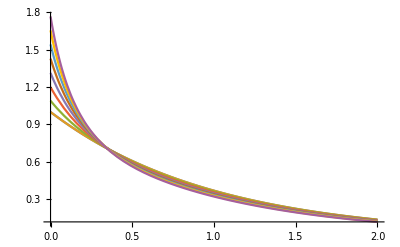

```mathematica
Plot[age,{t,0,2},PlotRange->All]
```

```mathematica
Integrate[MatrixExp[makeQ[3]*s].makeInject[3],{s,0,t}]/.t->.2
```

{-0.547102,0.165833,0.0154366,0.00329419}

```mathematica
Integrate[MatrixExp[makeQ[3]*(t-s)].makeInject[3],{s,0,t}]/.t->.2
```

{-0.547102,0.165833,0.0154366,0.00329419}

```mathematica
Integrate[Exp[-r*z],{z,s,t}]
```

(ⅇ^(-r s)-ⅇ^(-r t))/r

```mathematica
Solve[(ⅇ^(-r s)-ⅇ^(-r t))/r==u,s]//FullSimplify
```

{{s→ConditionalExpression[(2 ⅈ π C[1]+Log[1/(ⅇ^(-r t)+r u)])/r,C[1]∈Integers]}}

```mathematica
Exp[r*Log[1/(Exp[-r*t]+r*u)]/r]//FullSimplify
```

1/(ⅇ^(-r t)+r u)

```mathematica
Integrate[1/(a+r*u)^2*Exp[q*u],{u,0,1/r*(1-a)}]
```

ConditionalExpression[(ⅇ^(-(a q)/r) (-a ⅇ^(q/r) r+ⅇ^((a q)/r) r+a q ExpIntegralEi[q/r]-a q ExpIntegralEi[(a q)/r]))/(a r^2),((Im[a] (Im[q] Im[r]+Re[q] Re[r])≤(-1+Re[a]) (Im[r] Re[q]-Im[q] Re[r])&&(Im[r] Re[q]≥Im[q] Re[r]||Im[q] Re[a] Re[r]+Im[a] (Im[q] Im[r]+Re[q] Re[r])≥Im[r] Re[a] Re[q]||Im[a] (Im[q]^2+Re[q]^2)≤0))||(Im[a] (Im[q] Im[r]+Re[q] Re[r])≥(-1+Re[a]) (Im[r] Re[q]-Im[q] Re[r])&&(Im[a] (Im[q]^2+Re[q]^2)≥0||Im[r] Re[q]≤Im[q] Re[r]||Im[q] Re[a] Re[r]+Im[a] (Im[q] Im[r]+Re[q] Re[r])≤Im[r] Re[a] Re[q])))&&(a/(1-a)∉Reals||Re[a/(1-a)]<-1||(a/(-1+a)≠0&&Re[a/(1-a)]≥0))]

```mathematica
FullSimplify[(ⅇ^(-(a q)/r) (-a ⅇ^(q/r) r+ⅇ^((a q)/r) r+a q ExpIntegralEi[q/r]-a q ExpIntegralEi[(a q)/r]))/(a r^2),Assumptions->q≠0&&a>0]
```

(r/a-ⅇ^(-(a q)/r) (ⅇ^(q/r) r-q ExpIntegralEi[q/r]+q ExpIntegralEi[(a q)/r]))/r^2

```mathematica
Eigenvalues[makeQ[9]]
```

{-36,-28,-21,-15,-10,-6,-3,-1,0,0}

```mathematica
Table[Binomial[5,k],{k,0,5}]
```

{1,5,10,10,5,1}

```mathematica
FindSequenceFunction[{-21,-15,-10,-6,-3,-1,0},n]
```

1/2 (-56+15 n-n^2)

```mathematica
FindSequenceFunction[Reverse[{15,10,6,3,1,0}],n]
```

1/2 (-1+n) n

```mathematica
?Eigenvalues
```

Eigenvalues[m] gives a list of the eigenvalues of the square matrix m. 
Eigenvalues[{m,a}] gives the generalized eigenvalues of m with respect to a. 
Eigenvalues[m,k] gives the first k eigenvalues of m. 
Eigenvalues[{m,a},k] gives the first k generalized eigenvalues.

```mathematica
Eigenvectors[makeQ[5]]
```

{{-1,1,-1,1,-1,1},{5,-3,1,1,-3,5},{-20,6,1,-1,-6,20},{20,-2,-1,-1,-2,20},{0,0,0,0,0,1},{1,0,0,0,0,0}}

```mathematica
U =Transpose[ Eigenvectors[makeQ[5]]]
```

{{-1,5,-20,20,0,1},{1,-3,6,-2,0,0},{-1,1,1,-1,0,0},{1,1,-1,-1,0,0},{-1,-3,-6,-2,0,0},{1,5,20,20,1,0}}

```mathematica
d = DiagonalMatrix[Eigenvalues[makeQ[5]]]
```

{{-10,0,0,0,0,0},{0,-6,0,0,0,0},{0,0,-3,0,0,0},{0,0,0,-1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
U.d.Inverse[U]//MatrixForm
```

(0 | 10 | 0 | 0 | 0 | 0
0 | -4 | 6 | 0 | 0 | 0
0 | 1 | -6 | 3 | 0 | 0
0 | 0 | 3 | -6 | 1 | 0
0 | 0 | 0 | 6 | -4 | 0
0 | 0 | 0 | 0 | 10 | 0)

```mathematica
Ui = Inverse[U].makeInject[5]
```

{1/14,-1/10,1/14,-1/10,1,-1}

```mathematica
EUi = MatrixExp[d*t].Ui
```

{ⅇ^(-10 t)/14,-1/10 ⅇ^(-6 t),ⅇ^(-3 t)/14,-ⅇ^-t/10,1,-1}

```mathematica
U.EUi
```

{-1-ⅇ^(-10 t)/14-ⅇ^(-6 t)/2-(10 ⅇ^(-3 t))/7-2 ⅇ^-t,ⅇ^(-10 t)/14+(3 ⅇ^(-6 t))/10+(3 ⅇ^(-3 t))/7+ⅇ^-t/5,-1/14 ⅇ^(-10 t)-ⅇ^(-6 t)/10+ⅇ^(-3 t)/14+ⅇ^-t/10,ⅇ^(-10 t)/14-ⅇ^(-6 t)/10-ⅇ^(-3 t)/14+ⅇ^-t/10,-1/14 ⅇ^(-10 t)+(3 ⅇ^(-6 t))/10-(3 ⅇ^(-3 t))/7+ⅇ^-t/5,1+ⅇ^(-10 t)/14-ⅇ^(-6 t)/2+(10 ⅇ^(-3 t))/7-2 ⅇ^-t}

```mathematica
U//MatrixForm
```

(-1 | 5 | -20 | 20 | 0 | 1
1 | -3 | 6 | -2 | 0 | 0
-1 | 1 | 1 | -1 | 0 | 0
1 | 1 | -1 | -1 | 0 | 0
-1 | -3 | -6 | -2 | 0 | 0
1 | 5 | 20 | 20 | 1 | 0)

```mathematica
Integrate[1/Exp[-r*s],{s,0,t}]
```

(-1+ⅇ^(r t))/r

```mathematica
Integrate[Exp[r*z],{z,0,u}]
```

(-1+ⅇ^(r u))/r

```mathematica
eq = a*(k-1)/n+(1-2*a)*k/n+(1-a)*(k+1)/n==k/(n+1)
```

(a (-1+k))/n+((1-2 a) k)/n+((1-a) (1+k))/n==k/(1+n)

```mathematica
soln = Solve[eq,a]
```

{{a→(1+2 k+n+k n)/(2 (1+k) (1+n))}}

```mathematica
Integrate[Exp[(q+a*qs)*t]*λ*Exp[-λ*a],{a,0,∞}]
```

ConditionalExpression[-(ⅇ^(q t) λ)/(qs t-λ),Re[qs t]<Re[λ]]

```mathematica
Q=makeQ[3]; Qs = makeQs[3];
```

```mathematica
PseudoInverse[λ*IdentityMatrix[11]-Qs*t].λ*MatrixExp[Q*t].makeHet[10]/.{t->.2,λ->1}//MatrixForm
```

```mathematica
Integrate[MatrixExp[(Q+a*Qs)*t].makeHet[3]*λ*Exp[-λ*a],{a,0,∞}]
```

$Aborted

```mathematica
makePD[n_,m_]:=Table[Table[Binomial[j,i]*Binomial[n-j,m-i]/Binomial[n,m],{j,0,n}],{i,0,m}]
```

```mathematica
P = makePD[11,10]
```

{{1,1/11,0,0,0,0,0,0,0,0,0,0},{0,10/11,2/11,0,0,0,0,0,0,0,0,0},{0,0,9/11,3/11,0,0,0,0,0,0,0,0},{0,0,0,8/11,4/11,0,0,0,0,0,0,0},{0,0,0,0,7/11,5/11,0,0,0,0,0,0},{0,0,0,0,0,6/11,6/11,0,0,0,0,0},{0,0,0,0,0,0,5/11,7/11,0,0,0,0},{0,0,0,0,0,0,0,4/11,8/11,0,0,0},{0,0,0,0,0,0,0,0,3/11,9/11,0,0},{0,0,0,0,0,0,0,0,0,2/11,10/11,0},{0,0,0,0,0,0,0,0,0,0,1/11,1}}

```mathematica
P.Join[{0},Table[θ/i,{i,1,9}],{0}]
```

{(19 θ)/90,θ,θ/2,θ/3,θ/4,θ/5,θ/6,θ/7,θ/40}

```mathematica
Join[{0},Table[θ/i,{i,1,4}],{0}]
```

{0,θ,θ/2,θ/3,θ/4,0}

```mathematica
Join[{0},Table[θ/i,{i,1,4}],{0}].P
```

{0,(5 θ)/6,(2 θ)/3,(5 θ)/12,(11 θ)/36,(5 θ)/24,0}

```mathematica
PseudoInverse[P].Join[{0},Table[θ/i,{i,1,4}],{0}]//N
```

{-0.163618 θ,0.98171 θ,0.545725 θ,0.272367 θ,0.295725 θ,0.18171 θ,-0.030285 θ}

```mathematica
Join[{0},Table[θ/i,{i,1,11}],{0}]//N
```

{0.,θ,0.5 θ,0.333333 θ,0.25 θ,0.2 θ,0.166667 θ,0.142857 θ,0.125 θ,0.111111 θ,0.1 θ,0.0909091 θ,0.}

```mathematica
PseudoInverse[P].Join[{0},Table[θ/i,{i,1,9}],{0}]//N
```

{-0.0909048 θ,0.999953 θ,0.500235 θ,0.332629 θ,0.251408 θ,0.198028 θ,0.168638 θ,0.141449 θ,0.125704 θ,0.110876 θ,0.100047 θ,-0.00909518 θ}

```mathematica
Dimensions[PseudoInverse[P]]
```

{12,11}

```mathematica
Diagonal[PseudoInverse[P],1]//N
```

{-0.0999827,-0.243354,-0.4386,-0.630592,-0.654762,-0.434342,-0.16576,-0.0327147,-0.00285357,-0.0000779664}

```mathematica
PseudoInverse[P][[1,2]]
```

775841/705432

```mathematica
?Diagonal
```

Diagonal[m] gives the list of elements on the leading diagonal of the matrix m.
Diagonal[m,k] gives the elements on the k^th diagonal of m.

```mathematica
Pinv = PseudoInverse[P];
```

```mathematica
5*Pinv[[5]]-(10-5)*Pinv[[6]]//N
```

{-0.00561358,0.0684857,-0.392576,1.4208,4.13422,-7.85714,3.72293,-1.4208,0.392576,-0.0684857,0.00561358}

```mathematica
P.Pinv//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
makeNeut[n_]:=Join[{0},Table[θ/i,{i,1,n-1}],{0}]
```

```mathematica
P=makePD[6,5]
Pinv = PseudoInverse[P]
Pinv.makeNeut[5]+(IdentityMatrix[7]-Pinv.P).Table[w[i],{i,0,6}]//MatrixForm//N
```

{{1,1/6,0,0,0,0,0},{0,5/6,1/3,0,0,0,0},{0,0,2/3,1/2,0,0,0},{0,0,0,1/2,2/3,0,0},{0,0,0,0,1/3,5/6,0},{0,0,0,0,0,1/6,1}}

{{923/924,-887/4620,331/4620,-131/4620,37/4620,-1/924},{1/154,887/770,-331/770,131/770,-37/770,1/154},{-5/308,37/308,331/308,-131/308,37/308,-5/308},{5/231,-37/231,131/231,131/231,-37/231,5/231},{-5/308,37/308,-131/308,331/308,37/308,-5/308},{1/154,-37/770,131/770,-331/770,887/770,1/154},{-1/924,37/4620,-131/4620,331/4620,-887/4620,923/924}}

(-0.163618 θ+0.00108225 w[0.]-0.00649351 w[1.]+0.0162338 w[2.]-0.021645 w[3.]+0.0162338 w[4.]-0.00649351 w[5.]+0.00108225 w[6.]
0.98171 θ-0.00649351 w[0.]+0.038961 w[1.]-0.0974026 w[2.]+0.12987 w[3.]-0.0974026 w[4.]+0.038961 w[5.]-0.00649351 w[6.]
0.545725 θ+0.0162338 w[0.]-0.0974026 w[1.]+0.243506 w[2.]-0.324675 w[3.]+0.243506 w[4.]-0.0974026 w[5.]+0.0162338 w[6.]
0.272367 θ-0.021645 w[0.]+0.12987 w[1.]-0.324675 w[2.]+0.4329 w[3.]-0.324675 w[4.]+0.12987 w[5.]-0.021645 w[6.]
0.295725 θ+0.0162338 w[0.]-0.0974026 w[1.]+0.243506 w[2.]-0.324675 w[3.]+0.243506 w[4.]-0.0974026 w[5.]+0.0162338 w[6.]
0.18171 θ-0.00649351 w[0.]+0.038961 w[1.]-0.0974026 w[2.]+0.12987 w[3.]-0.0974026 w[4.]+0.038961 w[5.]-0.00649351 w[6.]
-0.030285 θ+0.00108225 w[0.]-0.00649351 w[1.]+0.0162338 w[2.]-0.021645 w[3.]+0.0162338 w[4.]-0.00649351 w[5.]+0.00108225 w[6.])

```mathematica
w = PseudoInverse[(IdentityMatrix[7]-Pinv.P)].(makeNeut[6]-Pinv.makeNeut[5])
```

{-(157 θ)/55440,(157 θ)/9240,-(157 θ)/3696,(157 θ)/2772,-(157 θ)/3696,(157 θ)/9240,-(157 θ)/55440}

```mathematica
Pinv.makeNeut[5]+(IdentityMatrix[7]-Pinv.P).w//N
```

{-0.16645 θ,0.998701 θ,0.503247 θ,0.329004 θ,0.253247 θ,0.198701 θ,-0.0331169 θ}

```mathematica
makeNeut[6]//N
```

{0.,θ,0.5 θ,0.333333 θ,0.25 θ,0.2 θ,0.}

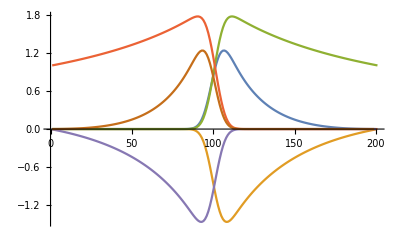

```mathematica
ListLinePlot[{Diagonal[PseudoInverse[makePD[201,200]],-3],Diagonal[PseudoInverse[makePD[201,200]],-2],Diagonal[PseudoInverse[makePD[201,200]],-1],Diagonal[PseudoInverse[makePD[201,200]]],Diagonal[PseudoInverse[makePD[201,200]],1],Diagonal[PseudoInverse[makePD[201,200]],2]}]
```

```mathematica
Qa[n_,i_,ip_]:=(n+1)*(4+i^2*(6+5*n+n^2)-i*(14+9n+n^2)-(n+4)*(2*i*(n+2)-n-5)*ip+(n^2+7n+12)*ip^2)
```

```mathematica
a[n_,i_]:=Qa[n,i,i-2]/(2*(n+2)*(n+3)*(n+4))
```

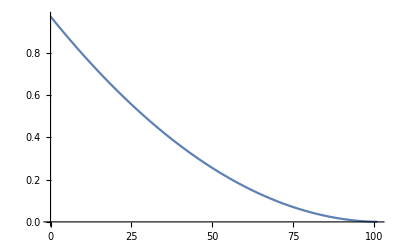

```mathematica
Plot[a[100,i],{i,0,101}]
```

```mathematica
Diagonal[PseudoInverse[makePD[51,50]]][[1;;10]]//N
```

{1.,1.02,1.04082,1.0625,1.08511,1.1087,1.13333,1.15909,1.18605,1.21429}

```mathematica
Diagonal[PseudoInverse[makePD[101,100]]][[1;;10]]//N
```

{1.,1.01,1.0202,1.03061,1.04124,1.05208,1.06316,1.07447,1.08602,1.09783}

```mathematica
Diagonal[PseudoInverse[makePD[201,200]]][[1;;10]]//N
```

{1.,1.005,1.01005,1.01515,1.0203,1.02551,1.03077,1.03608,1.04145,1.04688}

```mathematica
Diagonal[PseudoInverse[makePD[501,500]]][[1;;10]]//N
```

{1.,1.002,1.00401,1.00602,1.00805,1.01008,1.01212,1.01417,1.01623,1.01829}

```mathematica
D[x1*x2*x3*x4,x1,x2]
```

x3 x4

```mathematica
n-Binomial[n,2]//FullSimplify
```

-1/2 (-3+n) n

```mathematica
D[D[x[z],{z,0}],x[z]]
```

1

```mathematica
D[(x[z-dz]-2*x[z]+x[d+dz])/dz^2,x[z]]
```

-2/dz^2

```mathematica
makeQs[3]
```

{{0,-3,0,0},{0,1,-2,0},{0,0,2,-1},{0,0,0,3}}

```mathematica
a = D[MatrixExp[(makeQ[2]+s*makeQs[2])*t],s]//FullSimplify
```

{{0,(ⅇ^((-1+s) t) (ⅇ^(s t) (-1+2 (-1+s) t)+ⅇ^t (1+(-1+(3-2 s) s) t)))/(-1+s)^2,(ⅇ^((-1+s) t) (ⅇ^(s t) (-1+2 (-1+s) s t)+ⅇ^t (1+(-1+(3-2 s) s) t)))/(-1+s)^2},{0,(ⅇ^((-1+s) t) (ⅇ^(s t) (1-2 (-1+s) t)+ⅇ^t (-1+(-1+s) s t)))/(-1+s)^2,(ⅇ^((-1+s) t) (ⅇ^(s t) (1-2 (-1+s) s t)+ⅇ^t (-1+(-1+s) s t)))/(-1+s)^2},{0,(ⅇ^((-1+s) t) (ⅇ^(s t) (-1+2 (-1+s) t)+ⅇ^t (1+t-s t)))/(-1+s)^2,(ⅇ^((-1+s) t) (ⅇ^t (1+t-s t)+ⅇ^(s t) (-1+2 (-1+s) s t)))/(-1+s)^2}}

```mathematica
c = (makeQs[2]*t).MatrixExp[(makeQ[2]+s*makeQs[2])*t]//FullSimplify
```

{{0,(2 (ⅇ^((-1+2 s) t)-ⅇ^(s t) s) t)/(-1+s),(2 (-ⅇ^(s t)+ⅇ^((-1+2 s) t)) s t)/(-1+s)},{0,((-2 ⅇ^((-1+2 s) t)+ⅇ^(s t) (1+s)) t)/(-1+s),((-2 ⅇ^((-1+2 s) t) s+ⅇ^(s t) (1+s)) t)/(-1+s)},{0,(2 (-ⅇ^(s t)+ⅇ^((-1+2 s) t)) t)/(-1+s),(2 (-ⅇ^(s t)+ⅇ^((-1+2 s) t) s) t)/(-1+s)}}

```mathematica
b = Integrate[MatrixExp[(makeQ[2]+s*makeQs[2])*t*α].(makeQs[2]*t).MatrixExp[(makeQ[2]+s*makeQs[2])*t*(1-α)],{α,0,1}]//FullSimplify
```

{{0,-(ⅇ^(s t) (-1+t+s (-3+2 s) t+ⅇ^((-1+s) t) (1-2 (-1+s) t)))/(-1+s)^2,(ⅇ^(s t) (1+(-1+(3-2 s) s) t+ⅇ^((-1+s) t) (-1+2 (-1+s) s t)))/(-1+s)^2},{0,(ⅇ^((-1+s) t) (ⅇ^(s t) (1-2 (-1+s) t)+ⅇ^t (-1+(-1+s) s t)))/(-1+s)^2,(ⅇ^((-1+s) t) (ⅇ^(s t) (1-2 (-1+s) s t)+ⅇ^t (-1+(-1+s) s t)))/(-1+s)^2},{0,(ⅇ^((-1+s) t) (ⅇ^(s t) (-1+2 (-1+s) t)+ⅇ^t (1+t-s t)))/(-1+s)^2,(ⅇ^((-1+s) t) (ⅇ^t (1+t-s t)+ⅇ^(s t) (-1+2 (-1+s) s t)))/(-1+s)^2}}

```mathematica
a/c//FullSimplify
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{Indeterminate,(ⅇ^((-1+s) t) (ⅇ^(s t) (-1+2 (-1+s) t)+ⅇ^t (1+(-1+(3-2 s) s) t)))/(2 (-1+s) (ⅇ^((-1+2 s) t)-ⅇ^(s t) s) t),(ⅇ^((-1+s) t) (ⅇ^(s t) (-1+2 (-1+s) s t)+ⅇ^t (1+(-1+(3-2 s) s) t)))/(2 (-ⅇ^(s t)+ⅇ^((-1+2 s) t)) (-1+s) s t)},{Indeterminate,(ⅇ^((-1+s) t) (ⅇ^(s t) (1-2 (-1+s) t)+ⅇ^t (-1+(-1+s) s t)))/((-1+s) (-2 ⅇ^((-1+2 s) t)+ⅇ^(s t) (1+s)) t),(ⅇ^((-1+s) t) (ⅇ^(s t) (1-2 (-1+s) s t)+ⅇ^t (-1+(-1+s) s t)))/((-1+s) (-2 ⅇ^((-1+2 s) t) s+ⅇ^(s t) (1+s)) t)},{Indeterminate,1/2 (2+1/(-1+ⅇ^((-1+s) t))+1/(t-s t)),(ⅇ^((-1+s) t) (ⅇ^t (1+t-s t)+ⅇ^(s t) (-1+2 (-1+s) s t)))/(2 (-1+s) (-ⅇ^(s t)+ⅇ^((-1+2 s) t) s) t)}}

```mathematica
sfs[x_,γ_]:=2/(x*(1-x))*(1-Exp[-2*γ*(1-x)])/(1-Exp[-2*γ])
```

```mathematica
sampleSFS [n_,γ_]:=Table[Binomial[n,k]*NIntegrate[x^k*(1-x)^(n-k)*sfs[x,γ],{x,0,1}],{k,1,n-1}]
```

```mathematica
neut = sampleSFS[100,-.000001];
```

```mathematica
sel = sampleSFS[100,-1];
```

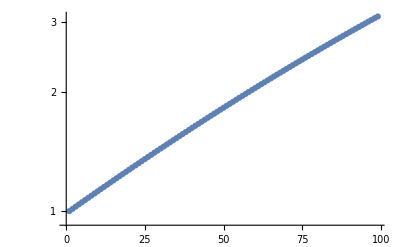

```mathematica
ListLogPlot[(neut/neut[[1]])/(sel/sel[[1]]),Ticks->Automatic]
```

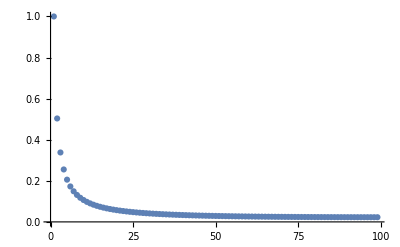

```mathematica
ListPlot[sel/sel[[1]],PlotRange->All]
```

```mathematica
neut[[1]]
```

3.83225×10^7 (1-x)^99 x

```mathematica
1/4^2*3/4
```

3/64

```mathematica
sfs[x_,γ_]:=2/(x*(1-x))*(1-Exp[-2*γ*(1-x)])/(1-Exp[-2*γ])
```

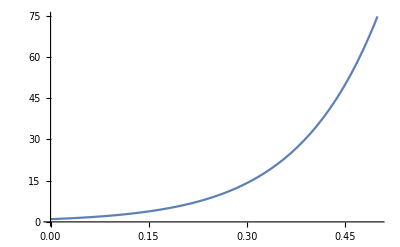

```mathematica
Plot[sfs[x,-.000000001]/sfs[x,-5],{x,0,.5}]
```

```mathematica
c
```

{{0,(2 (ⅇ^((-1+2 s) t)-ⅇ^(s t) s) t)/(-1+s),(2 (-ⅇ^(s t)+ⅇ^((-1+2 s) t)) s t)/(-1+s)},{0,((-2 ⅇ^((-1+2 s) t)+ⅇ^(s t) (1+s)) t)/(-1+s),((-2 ⅇ^((-1+2 s) t) s+ⅇ^(s t) (1+s)) t)/(-1+s)},{0,(2 (-ⅇ^(s t)+ⅇ^((-1+2 s) t)) t)/(-1+s),(2 (-ⅇ^(s t)+ⅇ^((-1+2 s) t) s) t)/(-1+s)}}

```mathematica
Clear[c]
```

```mathematica
Series[sfs[x,α]/sfs[x,c*α],{c,1,2}]
```

(1-ⅇ^(-2 (1-x) α))/(1-ⅇ^(-2 α+2 x α))+((1-ⅇ^(-2 (1-x) α)) ((2 ⅇ^(-2 α) α)/(1-ⅇ^(-2 α+2 x α))+(2 ⅇ^(2 α+2 x α) (1-ⅇ^(-2 α)) (-1+x) α)/((-ⅇ^(2 α)+ⅇ^(2 x α))^2)) (c-1))/(1-ⅇ^(-2 α))+((1-ⅇ^(-2 (1-x) α)) (-(2 ⅇ^(-2 α) α^2)/(1-ⅇ^(-2 α+2 x α))+(4 ⅇ^(2 x α) (-1+x) α^2)/((-ⅇ^(2 α)+ⅇ^(2 x α))^2)-(2 ⅇ^(2 α+2 x α) (1-ⅇ^(-2 α)) (ⅇ^(2 α)+ⅇ^(2 x α)) (-1+x)^2 α^2)/((-ⅇ^(2 α)+ⅇ^(2 x α))^3)) (c-1)^2)/(1-ⅇ^(-2 α))+O[c-1]^3

```mathematica
((1-ⅇ^(-2 (1-x) α)) ((2 ⅇ^(-2 α) α)/(1-ⅇ^(-2 α+2 x α))+(2 ⅇ^(2 α+2 x α) (1-ⅇ^(-2 α)) (-1+x) α)/((-ⅇ^(2 α)+ⅇ^(2 x α))^2)))/(1-ⅇ^(-2 α))//FullSimplify
```

```mathematica
(1-ⅇ^(-2 (1-x) α))/(1-ⅇ^(-2 α+2 x α))//FullSimplify
```

1

```mathematica
Series[ϕ[α]/ϕ[c*α]*f[α],{α,0,2}]
```

f[0]+(f'[0]+(f[0] ϕ'[0])/ϕ[0]-(c f[0] ϕ'[0])/ϕ[0]) α+((2 ϕ[0] f'[0] ϕ'[0]-2 c ϕ[0] f'[0] ϕ'[0]-2 c f[0] ϕ'[0]^2+2 c^2 f[0] ϕ'[0]^2+ϕ[0]^2 f''[0]+f[0] ϕ[0] ϕ''[0]-c^2 f[0] ϕ[0] ϕ''[0]) α^2)/(2 ϕ[0]^2)+O[α]^3

```mathematica
(2 ϕ[0] f'[0] ϕ'[0]-2 c ϕ[0] f'[0] ϕ'[0]-2 c f[0] ϕ'[0]^2+2 c^2 f[0] ϕ'[0]^2+ϕ[0]^2 f''[0]+f[0] ϕ[0] ϕ''[0]-c^2 f[0] ϕ[0] ϕ''[0])//FullSimplify
```

2 (-1+c) c f[0] ϕ'[0]^2+ϕ[0]^2 f''[0]-(-1+c) ϕ[0] (2 f'[0] ϕ'[0]+(1+c) f[0] ϕ''[0])